Quartic Covariant Galileon

```mathematica
Quit[]
```

```mathematica
s=.
HoverH0equation=1-x^-2(OmegaM0/a+OmegaR0/a^2)-(a/x)^(2(1+s))(OmegaPhi0); (*x is conformal H over H_0*)
Solution=NSolve[HoverH0equation==0,x]
```

$Aborted

```mathematica
?NSolve
```

NSolve[expr,vars] attempts to find numerical approximations to the solutions of the system expr of equations or inequalities for the variables vars. 
NSolve[expr,vars,Reals] finds solutions over the domain of real numbers.

```mathematica
(*OmegaM0=0.293;
OmegaR0=10^(-5);
OmegaPhi0=1-OmegaM0-OmegaR0*)
OmegaM0=0.293
OmegaR0=8.32*10^(-5)(*10^(-5)*)(*8.32*10^(-5)*)
OmegaPhi0=1-OmegaM0-OmegaR0
s=1
a=.
HoverH0equation=1-x^-2(OmegaM0/a+OmegaR0/a^2)-(a/x)^(2(1+s))(OmegaPhi0); (*x is conformal H over H_0*)
Solution=NSolve[HoverH0equation==0,x]
a=1
Solution (*Looking at this I know the right solution is the fourth one*)
```

0.293

0.0000832

0.706917

1

{{x→-7.83741×10^-9 √((6.77249×10^11)/a^2+(2.38502×10^15)/a-(114123. √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))/a^2)},{x→7.83741×10^-9 √((6.77249×10^11)/a^2+(2.38502×10^15)/a-(114123. √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))/a^2)},{x→-7.83741×10^-9 √((6.77249×10^11)/a^2+(2.38502×10^15)/a+(114123. √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))/a^2)},{x→7.83741×10^-9 √((6.77249×10^11)/a^2+(2.38502×10^15)/a+(114123. √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))/a^2)}}

1

{{x→0.-0.840783 ⅈ},{x→0.+0.840783 ⅈ},{x→-1.},{x→1.}}

```mathematica
0.00223606797749979 √(1/a^2+29300./a+(√(1.+58600. a+8.5849*^8 a^2+2.82796*^10 a^8))/a^2)
```

```mathematica
{{x->-7.837410259793203*^-9 √((6.77248681876*^11)/a^2+(2.385022401318125*^15)/a-(114122.79839278391 √(3.5216931457552*^13+2.48042329737085*^17 a+4.367572272413816*^20 a^2+1.43857713640625*^22 a^8))/a^2)},{x->7.837410259793203*^-9 √((6.77248681876*^11)/a^2+(2.385022401318125*^15)/a-(114122.79839278391 √(3.5216931457552*^13+2.48042329737085*^17 a+4.367572272413816*^20 a^2+1.43857713640625*^22 a^8))/a^2)},{x->-7.837410259793203*^-9 √((6.77248681876*^11)/a^2+(2.385022401318125*^15)/a+(114122.79839278391 √(3.5216931457552*^13+2.48042329737085*^17 a+4.367572272413816*^20 a^2+1.43857713640625*^22 a^8))/a^2)},{x->.03}}
```

1

{{x→0.-0.840783 ⅈ},{x→0.+0.840783 ⅈ},{x→-1.},{x→1.}}

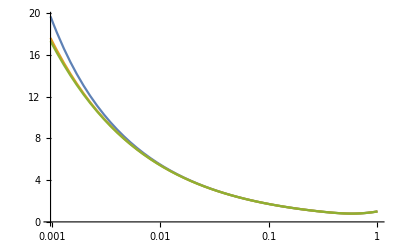

```mathematica
LogLinearPlot[{7.837410259793203*^-9 √((6.77248681876*^11)/a^2+(2.385022401318125*^15)/a+(114122.79839278391 √(3.5216931457552*^13+2.48042329737085*^17 a+4.367572272413816*^20 a^2+1.43857713640625*^22 a^8))/a^2),0.00223606797749979 √(1/a^2+29300./a+(√(1.+58600. a+8.5849*^8 a^2+2.82796*^10 a^8))/a^2),0.022360679774997897 √(293./a+(√(85849.+2.828*^6 a^6))/a)},{a,0,1}]
```

```mathematica
OmegaM0=.
OmegaR0=.
OmegaPhi0=.
a=.
HoverH0equation=1-x^-2(OmegaM0/a+OmegaR0/a^2)-(a/x)^(2(1+1))(OmegaPhi0); (*x is conformal H over H_0*);
Solution=NSolve[HoverH0equation==0,x]
a=1;
OmegaM0=0.293;
OmegaR0=8.32*10^(-5)(*10^(-5)*)(*8.32*10^(-5)*);
OmegaPhi0=1-OmegaM0-OmegaR0;
Solution
OmegaM0=.
OmegaR0=.
OmegaPhi0=.
a=.
FortranForm[√((0.5 OmegaM0)/a+(0.5 √(4. a^8 OmegaPhi0+(-1. a OmegaM0-1. OmegaR0)^2))/a^2+(0.5 OmegaR0)/a^2)]
```

{{x→-1. √((0.5 OmegaM0)/a+(0.5 √(4. a^8 OmegaPhi0+(-1. a OmegaM0-1. OmegaR0)^2))/a^2+(0.5 OmegaR0)/a^2)},{x→√((0.5 OmegaM0)/a+(0.5 √(4. a^8 OmegaPhi0+(-1. a OmegaM0-1. OmegaR0)^2))/a^2+(0.5 OmegaR0)/a^2)},{x→-0.707107 √(OmegaM0/a+OmegaR0/a^2-(1. √(a^2 OmegaM0^2+4. a^8 OmegaPhi0+2. a OmegaM0 OmegaR0+OmegaR0^2))/a^2)},{x→0.707107 √(OmegaM0/a+OmegaR0/a^2-(1. √(a^2 OmegaM0^2+4. a^8 OmegaPhi0+2. a OmegaM0 OmegaR0+OmegaR0^2))/a^2)}}

{{x→-1.},{x→1.},{x→0.-0.840783 ⅈ},{x→0.+0.840783 ⅈ}}

Sqrt((0.5*OmegaM0)/a + (0.5*Sqrt(4.*a**8*OmegaPhi0 + (-1.*a*OmegaM0 - 1.*OmegaR0)**2))/a**2 + (0.5*OmegaR0)/a**2)

```mathematica
a=.
HconfOverH0=7.837410259793203*^-9 √((6.77248681876*^11)/a^2+(2.385022401318125*^15)/a+1/a^2 114122.79839278391 √(3.5216931457552*^13+2.48042329737085*^17 a+4.367572272413816*^20 a^2+1.43857713640625*^22 a^8))
FortranForm[%]
HLCDM = Sqrt[OmegaM0/a+OmegaR0/a^2+a^2 *OmegaPhi0]
```

7.83741×10^-9 √((6.77249×10^11)/a^2+(2.38502×10^15)/a+(114123. √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))/a^2)

√(0.0000832/a^2+0.293/a+0.706917 a^2)

7.837410259793203e-9*Sqrt(6.77248681876e11/a**2 + 2.385022401318125e15/a + (114122.79839278391*Sqrt(3.5216931457552e13 + 2.48042329737085e17*a + 4.367572272413816e20*a**2 + 1.43857713640625e22*a**8))/a**2)

```mathematica
HcoH0 = √((0.5 OmegaM0)/a+(0.5 √(4. a^8 OmegaPhi0+(-1. a OmegaM0-1. OmegaR0)^2))/a^2+(0.5 OmegaR0)/a^2)
FortranForm[%]
```

1.

1.

```mathematica
HconfOverH0P=D[HcoH0,a];
FortranForm[%]
```

((-0.5*OmegaM0)/a**2 + (0.25*(32.*a**7*OmegaPhi0 - 2.*OmegaM0*(-1.*a*OmegaM0 - 1.*OmegaR0)))/(a**2*Sqrt(4.*a**8*OmegaPhi0 + (-1.*a*OmegaM0 - 1.*OmegaR0)**2)) - 
     -    (1.*Sqrt(4.*a**8*OmegaPhi0 + (-1.*a*OmegaM0 - 1.*OmegaR0)**2))/a**3 - (1.*OmegaR0)/a**3)/
     -  (2.*Sqrt((0.5*OmegaM0)/a + (0.5*Sqrt(4.*a**8*OmegaPhi0 + (-1.*a*OmegaM0 - 1.*OmegaR0)**2))/a**2 + (0.5*OmegaR0)/a**2))

```mathematica
HconfOverH0PP=D[HconfOverH0P,a];
FortranForm[%]
```

-((-0.5*OmegaM0)/a**2 + (0.25*(32.*a**7*OmegaPhi0 - 2.*OmegaM0*(-1.*a*OmegaM0 - 1.*OmegaR0)))/(a**2*Sqrt(4.*a**8*OmegaPhi0 + (-1.*a*OmegaM0 - 1.*OmegaR0)**2)) - 
     -       (1.*Sqrt(4.*a**8*OmegaPhi0 + (-1.*a*OmegaM0 - 1.*OmegaR0)**2))/a**3 - (1.*OmegaR0)/a**3)**2/
     -   (4.*((0.5*OmegaM0)/a + (0.5*Sqrt(4.*a**8*OmegaPhi0 + (-1.*a*OmegaM0 - 1.*OmegaR0)**2))/a**2 + (0.5*OmegaR0)/a**2)**1.5) + 
     -  ((1.*OmegaM0)/a**3 - (0.125*(32.*a**7*OmegaPhi0 - 2.*OmegaM0*(-1.*a*OmegaM0 - 1.*OmegaR0))**2)/(a**2*(4.*a**8*OmegaPhi0 + (-1.*a*OmegaM0 - 1.*OmegaR0)**2)**1.5) + 
     -     (0.25*(2.*OmegaM0**2 + 224.*a**6*OmegaPhi0))/(a**2*Sqrt(4.*a**8*OmegaPhi0 + (-1.*a*OmegaM0 - 1.*OmegaR0)**2)) - 
     -     (1.*(32.*a**7*OmegaPhi0 - 2.*OmegaM0*(-1.*a*OmegaM0 - 1.*OmegaR0)))/(a**3*Sqrt(4.*a**8*OmegaPhi0 + (-1.*a*OmegaM0 - 1.*OmegaR0)**2)) + 
     -     (3.*Sqrt(4.*a**8*OmegaPhi0 + (-1.*a*OmegaM0 - 1.*OmegaR0)**2))/a**4 + (3.*OmegaR0)/a**4)/
     -   (2.*Sqrt((0.5*OmegaM0)/a + (0.5*Sqrt(4.*a**8*OmegaPhi0 + (-1.*a*OmegaM0 - 1.*OmegaR0)**2))/a**2 + (0.5*OmegaR0)/a**2))

```mathematica
HconfOverH0PPP=D[HconfOverH0PP,a];
FortranForm[%]
```

(3*((-0.5*OmegaM0)/a**2 + (0.25*(32.*a**7*OmegaPhi0 - 2.*OmegaM0*(-1.*a*OmegaM0 - 1.*OmegaR0)))/(a**2*Sqrt(4.*a**8*OmegaPhi0 + (-1.*a*OmegaM0 - 1.*OmegaR0)**2)) - 
     -        (1.*Sqrt(4.*a**8*OmegaPhi0 + (-1.*a*OmegaM0 - 1.*OmegaR0)**2))/a**3 - (1.*OmegaR0)/a**3)**3)/
     -   (8.*((0.5*OmegaM0)/a + (0.5*Sqrt(4.*a**8*OmegaPhi0 + (-1.*a*OmegaM0 - 1.*OmegaR0)**2))/a**2 + (0.5*OmegaR0)/a**2)**2.5) - 
     -  (3*((1.*OmegaM0)/a**3 - (0.125*(32.*a**7*OmegaPhi0 - 2.*OmegaM0*(-1.*a*OmegaM0 - 1.*OmegaR0))**2)/(a**2*(4.*a**8*OmegaPhi0 + (-1.*a*OmegaM0 - 1.*OmegaR0)**2)**1.5) + 
     -       (0.25*(2.*OmegaM0**2 + 224.*a**6*OmegaPhi0))/(a**2*Sqrt(4.*a**8*OmegaPhi0 + (-1.*a*OmegaM0 - 1.*OmegaR0)**2)) - 
     -       (1.*(32.*a**7*OmegaPhi0 - 2.*OmegaM0*(-1.*a*OmegaM0 - 1.*OmegaR0)))/(a**3*Sqrt(4.*a**8*OmegaPhi0 + (-1.*a*OmegaM0 - 1.*OmegaR0)**2)) + 
     -       (3.*Sqrt(4.*a**8*OmegaPhi0 + (-1.*a*OmegaM0 - 1.*OmegaR0)**2))/a**4 + (3.*OmegaR0)/a**4)*
     -     ((-0.5*OmegaM0)/a**2 + (0.25*(32.*a**7*OmegaPhi0 - 2.*OmegaM0*(-1.*a*OmegaM0 - 1.*OmegaR0)))/(a**2*Sqrt(4.*a**8*OmegaPhi0 + (-1.*a*OmegaM0 - 1.*OmegaR0)**2)) - 
     -       (1.*Sqrt(4.*a**8*OmegaPhi0 + (-1.*a*OmegaM0 - 1.*OmegaR0)**2))/a**3 - (1.*OmegaR0)/a**3))/
     -   (4.*((0.5*OmegaM0)/a + (0.5*Sqrt(4.*a**8*OmegaPhi0 + (-1.*a*OmegaM0 - 1.*OmegaR0)**2))/a**2 + (0.5*OmegaR0)/a**2)**1.5) + 
     -  ((-3.*OmegaM0)/a**4 + (0.1875*(32.*a**7*OmegaPhi0 - 2.*OmegaM0*(-1.*a*OmegaM0 - 1.*OmegaR0))**3)/(a**2*(4.*a**8*OmegaPhi0 + (-1.*a*OmegaM0 - 1.*OmegaR0)**2)**2.5) - 
     -     (0.375*(2.*OmegaM0**2 + 224.*a**6*OmegaPhi0)*(32.*a**7*OmegaPhi0 - 2.*OmegaM0*(-1.*a*OmegaM0 - 1.*OmegaR0)))/(a**2*(4.*a**8*OmegaPhi0 + (-1.*a*OmegaM0 - 1.*OmegaR0)**2)**1.5) + 
     -     (0.75*(32.*a**7*OmegaPhi0 - 2.*OmegaM0*(-1.*a*OmegaM0 - 1.*OmegaR0))**2)/(a**3*(4.*a**8*OmegaPhi0 + (-1.*a*OmegaM0 - 1.*OmegaR0)**2)**1.5) + 
     -     (336.*a**3*OmegaPhi0)/Sqrt(4.*a**8*OmegaPhi0 + (-1.*a*OmegaM0 - 1.*OmegaR0)**2) - (1.5*(2.*OmegaM0**2 + 224.*a**6*OmegaPhi0))/(a**3*Sqrt(4.*a**8*OmegaPhi0 + (-1.*a*OmegaM0 - 1.*OmegaR0)**2)) + 
     -     (4.5*(32.*a**7*OmegaPhi0 - 2.*OmegaM0*(-1.*a*OmegaM0 - 1.*OmegaR0)))/(a**4*Sqrt(4.*a**8*OmegaPhi0 + (-1.*a*OmegaM0 - 1.*OmegaR0)**2)) - 
     -     (12.*Sqrt(4.*a**8*OmegaPhi0 + (-1.*a*OmegaM0 - 1.*OmegaR0)**2))/a**5 - (12.*OmegaR0)/a**5)/
     -   (2.*Sqrt((0.5*OmegaM0)/a + (0.5*Sqrt(4.*a**8*OmegaPhi0 + (-1.*a*OmegaM0 - 1.*OmegaR0)**2))/a**2 + (0.5*OmegaR0)/a**2))

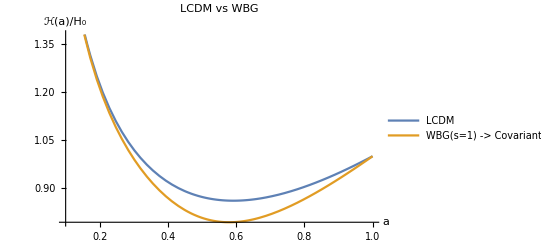

```mathematica
Plot[{HLCDM,HconfOverH0},{a,0.1,1}, PlotLegends->{"LCDM","WBG(s=1) -> Covariant Galileon"}, AxesLabel->{Style["a",FontSize->20],Style["ℋ(a)/H_0",FontSize->20]},PlotLabel->Style["LCDM vs WBG", FontSize->30]]
```

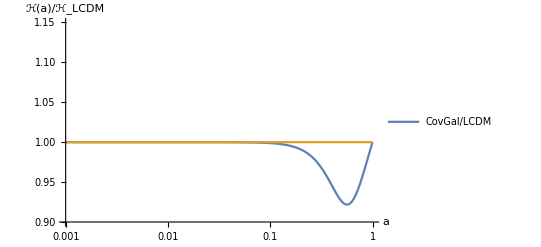

```mathematica
LogLinearPlot[{ HconfOverH0/HLCDM,HLCDM/HLCDM },{a,0.001,1}, PlotLegends->{"CovGal/LCDM"}, AxesLabel->{Style["a",FontSize->20],Style["ℋ(a)/ℋ_LCDM",FontSize->20]},PlotLabel->Style[" ", FontSize->30], PlotRange->{{0.001,1},{0.9,1.15}}]
```

Let’s find X(a)

```mathematica
a=.
XoverXds = (   (1-OmegaM0-OmegaR0)^( 1/(2(s+1)) ) HconfOverH0^(-1) a )^(1/q)/.p->1/.q->1/2//PowerExpand//Simplify
```

(1.3688×10^16 a^4)/(6.77249×10^11+2.38502×10^15 a+114123. √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))

```mathematica
(*XLCDM = 
Xs0 =69998.99999999997 (a^2/(√(1.+30000. a+69999. a^4)))^2.
Xs0p5 =0.7883660079734442 (a/(-(1.2599210498948732 (-1.-30000. a))/((1.889973*^16 a^9+√(1.08*^17 (-1.-30000. a)^3 a^6+3.571997940729*^32 a^18))^(1/3))+1/a^2 2.645668419946999*^-6 (1.889973*^16 a^9+√(1.08*^17 (-1.-30000. a)^3 a^6+3.571997940729*^32 a^18))^(1/3)))^2.
Xsm0p5=1.9599440004000008*^10 (a^3/(69999. a^3+√(-400000. (-1.-30000. a) a^2+4.899860001*^9 a^6)))^2.
Xs1 = 167330.81007393703 (a/(√(1/a^2+30000./a+(√(1.+60000. a+9.*^8 a^2+2.79996*^10 a^8))/a^2)))^2.
Xs1o5 = 10.824004689806106 (a/(√(1/a^2+30000./a+(√(1.+60000. a+9.*^8 a^2+2.79996*^10 a^8))/a^2)))^(2/5)*)
```

```mathematica
dataEFTCAMBChi=Import[FileNameJoin[{NotebookDirectory[],"fort.22"}]];
dataEFTCAMBadotoa=Import[FileNameJoin[{NotebookDirectory[],"fort.21"}]];
```

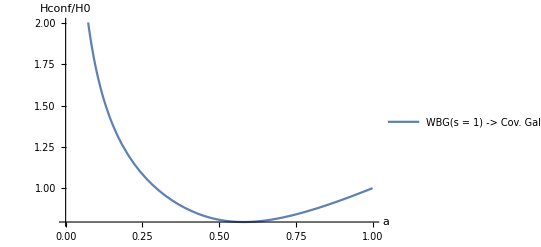

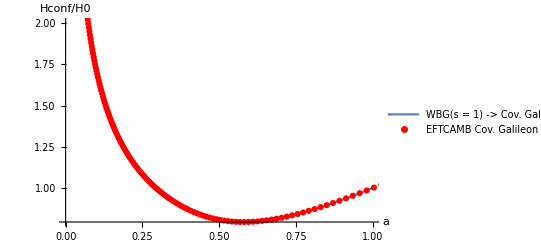

```mathematica
nbPlotH=Plot[{HconfOverH0},{a,0,1}, PlotLegends->{"WBG(s = 1) -> Cov. Galileon"}, AxesLabel->{Style["a",FontSize->20],Style["Hconf/H0",FontSize->20]}]
EFTCAMBPlotH = ListPlot[
dataEFTCAMBadotoa⟦All,{1,2}⟧
,Joined->False
,PlotMarkers->Automatic, PlotRange->{{0,1},{-0.15,2}}, PlotStyle->Red, PlotLegends->{"EFTCAMB Cov. Galileon"}
];
Show[nbPlotH,EFTCAMBPlotH]
```

```mathematica
nbPlot=Plot[{XoverXds},{a,0,1}, PlotLegends->{"WBG(s = 1) -> Cov. Galileon"}, AxesLabel->{Style["a",FontSize->20],Style["Χ(a)/Χ_DS",FontSize->20]}];
EFTCAMBPlot = ListPlot[
dataEFTCAMBChi⟦All,{1,2}⟧
,Joined->False
,PlotMarkers->Automatic, PlotRange->{{0,1},{-0.15,2}}, PlotStyle->Red, PlotLegends->{"EFTCAMB Cov. Galileon"}, PlotLabel->"Chi(a)"
];
Show[nbPlot,EFTCAMBPlot]
```

lets calculate Phi prime (derivative of phi w.r.t. scale factor a)

```mathematica
Sqrt[-XoverXds Xds]/HconfOverH0//PowerExpand//Simplify
```

((0.+1.49278×10^16 ⅈ) √(6.77249×10^11+2.38502×10^15 a+114123. √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8)) √Xds)/(((6.77249×10^11+2.38502×10^15 a+114123. √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))/a^2)^(3/2))

EFT functions plots

Covariant Galileon

```mathematica
p=.
q=.
s=.
CovGal = {s->1,p->1, q->1/2}
```

{s→1,p→1,q→1/2}

```mathematica
c4=.
c5=0;
DeSitterFP = {Subscript[c, 2]->3-6 Subscript[c, 4]-24 Subscript[c, 5]+12 Subscript[c, 4] p+24 Subscript[c, 4] q,Subscript[c, 3]->(√2 p)/(-1+2 p+2 q)-(4 √2 Subscript[c, 4] p)/(-1+2 p+2 q)-(16 √2 Subscript[c, 5] p)/(-1+2 p+2 q)+(8 √2 Subscript[c, 4] p^2)/(-1+2 p+2 q)-(4 √2 Subscript[c, 4] q)/(-1+2 p+2 q)-(16 √2 Subscript[c, 5] q)/(-1+2 p+2 q)+(24 √2 Subscript[c, 4] p q)/(-1+2 p+2 q)+(16 √2 Subscript[c, 4] q^2)/(-1+2 p+2 q)}
```

{c2→3-6 c4+12 c4 p+24 c4 q,c3→(√2 p)/(-1+2 p+2 q)-(4 √2 c4 p)/(-1+2 p+2 q)+(8 √2 c4 p^2)/(-1+2 p+2 q)-(4 √2 c4 q)/(-1+2 p+2 q)+(24 √2 c4 p q)/(-1+2 p+2 q)+(16 √2 c4 q^2)/(-1+2 p+2 q)}

Let’s find the values for c4 and Xds from Simone’s paper

```mathematica
Solve[{Xds==(2 (3+6 d4-24 c5+12 d4 p) Hds^2M^2)/(c2),d4==-(c4 Xds^2)/(4M^4 H0^4)},{Xds,d4}]/.Hds-> H0(1-OmegaM0-OmegaR0)^(1/4)/.p->1/.q -> 1/2/.c5->0/.c2->-1/.c4->-1/9 xi^(-2)+2/3(1-OmegaM0-OmegaR0) xi^(-4)/.xi->2.53//FullSimplify;
%/.√(H0^4)-> H0^2
```

{{Xds→-7.61302 H0^2 M^2,d4→0.084852},{Xds→-14.9535 H0^2 M^2,d4→0.327367}}

```mathematica
Solve[{Xds==(2 (3-6 d4-24 c5+12 d4 p+24d4 q) Hds^2M^2)/(c2),d4==-(c4 Xds^2)/(4M^4 H0^4)},{Xds,d4}]/.Hds-> H0(1-OmegaM0-OmegaR0)^(1/4)/.p->1/.q -> 1/2/.c5->0/.c2->-1/.c4->-1/9 xi^(-2)+2/3(1-OmegaM0-OmegaR0) xi^(-4)/.xi->2.53//FullSimplify;
%/.√(H0^4)-> H0^2
```

{{Xds→-5.43628 H0^2 M^2,d4→0.0452671},{Xds→-60.0467 H0^2 M^2,d4→5.52277}}

```mathematica
(1-OmegaM0-OmegaR0)^(1/4)d4->0.045267108772803155
```

0.911498 d4→0.0452671

Common substitutions:

```mathematica
Hc=HconfOverH0 H0//Simplify
HcP = D[Hc,a]//Simplify
HcPP = D[HcP,a]//Simplify
HcPPP = D[HcPP,a]//Simplify
X = XoverXds Xds//Simplify
PhiP = Sqrt[-X]/Hc//Simplify
PhiPP = D[PhiP,a]//Simplify
PhiPPP = D[PhiPP,a]//Simplify
PhiPPPP = D[PhiPPP,a]//Simplify
(*adot = Hc a//Simplify
adotdot = Hc a^2 HcP + Hc adot//Simplify*)
```

7.83741×10^-9 √((6.77249×10^11+2.38502×10^15 a+114123. √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))/a^2) H0

(3.91871×10^-9 (-1.3545×10^12-2.38502×10^15 a+(a (1.41536×10^22+4.9844×10^25 a+6.56698×10^27 a^7))/(√(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))-228246. √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8)) H0)/(a^3 √((6.77249×10^11+2.38502×10^15 a+114123. √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))/a^2))

((2.6332×10^31+5.34856×10^48 a^5+1.05701×10^51 a^11+6.5908×10^48 a^16+1.16052×10^52 a^17+4.43719×10^24 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8)+a (4.17292×10^35+5.46916×10^28 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^2 (2.57172×10^39+2.40755×10^32 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^8 (4.84036×10^40+7.25019×10^33 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^3 (7.61908×10^42+4.36037×10^35 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^9 (4.2615×10^44+3.82988×10^37 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^4 (1.06314×10^46+2.55927×10^38 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^10 (1.20059×10^48+4.63631×10^40 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))) H0)/(a^4 (3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8)^(3/2) (5.93439×10^6+2.08987×10^10 a+1. √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8)) √((6.77249×10^11+2.38502×10^15 a+114123. √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))/a^2))

((-3.91893×10^59+8.06531×10^92 a^15-9.4362×10^94 a^21-3.65494×10^96 a^27-6.81985×10^93 a^32-9.6068×10^96 a^33-6.60378×10^52 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8)+a^26 (-4.59658×10^93-7.93756×10^85 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^20 (-1.91258×10^92-5.34939×10^84 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^25 (-1.74032×10^90-7.62873×10^82 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^19 (-1.37915×10^89-8.58013×10^81 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^8 (-3.47659×10^88-4.88199×10^80 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^24 (-2.07021×10^86-1.57545×10^79 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^18 (-4.64803×10^85-4.6785×10^78 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^7 (-4.85378×10^85-1.52491×10^78 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^6 (-3.76573×10^82-1.88951×10^75 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^17 (-7.48443×10^81-1.06959×10^75 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^5 (-1.81889×10^79-1.26535×10^72 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^16 (-4.65925×10^77-8.81547×10^70 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^4 (-5.72623×10^75-5.11029×10^68 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^3 (-1.18207×10^72-1.28888×10^65 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^2 (-1.5492×10^68-1.9963×10^61 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a (-1.17309×10^64-1.74421×10^57 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^9 (-1.02027×10^91+6.17492×10^65 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^10 (1.8985×10^76+4.01461×10^69 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^11 (8.04045×10^79+1.52057×10^73 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^12 (2.55455×10^83+3.82493×10^76 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^13 (6.50328×10^86+6.16423×10^79 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^14 (1.08785×10^90+4.66324×10^82 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))) H0)/(a^5 (3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8)^(5/2) (5.93439×10^6+2.08987×10^10 a+1. √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))^3 √((6.77249×10^11+2.38502×10^15 a+114123. √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))/a^2))

(1.3688×10^16 a^4 Xds)/(6.77249×10^11+2.38502×10^15 a+114123. √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))

(1.49278×10^16 √(-(1. a^4 Xds)/(6.77249×10^11+2.38502×10^15 a+114123. √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))))/(√((6.77249×10^11+2.38502×10^15 a+114123. √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))/a^2) H0)

(5.89536×10^-21 a^3 (-3.30216×10^59-3.38598×10^73 a^4-5.57632×10^74 a^10+4.59177×10^75 a^16-5.56446×10^52 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8)+a^3 (-4.32666×10^70-1.62018×10^63 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^8 (-7.86859×10^67-1.89419×10^60 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^2 (-2.04766×10^67-1.61023×10^60 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a (-4.26397×10^63-5.22559×10^56 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^9 (-4.35447×10^71+4.3845×10^48 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))) Xds)/(√(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8) (5.93439×10^6+2.08987×10^10 a+1. √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))^4 √((6.77249×10^11+2.38502×10^15 a+114123. √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))/a^2) H0 √(-(1. a^4 Xds)/(6.77249×10^11+2.38502×10^15 a+114123. √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))))

-((1. a^2 (2.29249×10^74-7.86338×10^107 a^15-5.18003×10^109 a^21-6.78918×10^110 a^27-7.02471×10^110 a^33+3.86306×10^67 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8)+a^26 (-7.27738×10^107-1.03751×10^100 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^20 (-8.34745×10^106-1.73504×10^99 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^14 (-1.6821×10^105-4.26429×10^97 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^25 (-2.4706×10^104-8.50026×10^96 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^19 (-5.25581×10^103-2.31677×10^96 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^13 (-1.5048×10^102-7.97759×10^94 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^24 (-2.70202×10^100-1.56344×10^93 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^18 (-1.62488×10^100-1.12421×10^93 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^12 (-7.32175×10^98-6.06779×10^91 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^17 (-2.47538×10^96-2.36939×10^89 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^11 (-2.09612×10^95-2.41221×10^88 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^16 (-1.49029×10^92-1.83982×10^85 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^10 (-3.53256×10^91-5.30034×10^84 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^9 (6.36627×10^105-6.11294×10^80 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a (6.45865×10^78+9.52301×10^71 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^2 (8.05552×10^82+1.02207×10^76 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^3 (5.8406×10^86+6.24261×10^79 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^4 (2.71504×10^90+2.37667×10^83 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^5 (8.40241×10^93+5.78909×10^86 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^6 (1.7346×10^97+8.84258×10^89 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^7 (2.30998×10^100+7.78508×10^92 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^8 (1.80776×10^103+3.04625×10^95 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^32 (-5.31928×10^107+1.12044×10^100 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))) Xds)/((3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8)^(3/2) (5.93439×10^6+2.08987×10^10 a+1. √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))^7 √((6.77249×10^11+2.38502×10^15 a+114123. √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))/a^2) H0 √(-(1. a^4 Xds)/(6.77249×10^11+2.38502×10^15 a+114123. √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8)))))

-((1. a (1.34982×10^109+6.161×10^165 a^38+1.03771×10^167 a^44+3.20529×10^167 a^50-1.00071×10^167 a^56+2.27458×10^102 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8)+a^25 (-5.16025×10^160-5.53351×10^152 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^19 (-1.04682×10^159-1.34399×10^151 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^24 (-7.43307×10^157-1.61282×10^150 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^18 (-1.78959×10^156-4.62738×10^148 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^23 (-6.35145×10^154-2.10343×10^147 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^29 (-3.51733×10^155-6.77075×10^146 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^17 (-1.85296×10^153-7.24918×10^145 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^28 (-1.60419×10^152-1.62081×10^144 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^22 (-3.55729×10^151-1.60304×10^144 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^16 (-1.29283×10^150-6.80899×10^142 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^27 (-4.60108×10^148-9.58576×10^140 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^21 (-1.36251×10^148-7.84116×10^140 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^15 (-6.3988×10^146-4.25549×10^139 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^26 (-1.61901×10^163-2.69853×10^137 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^20 (-2.80878×10^161-2.5476×10^137 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^14 (-1.21943×10^143-1.85662×10^136 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^13 (-2.85805×10^140-1.31003×10^132 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^12 (-1.30249×10^138-5.53488×10^129 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^11 (1.39464×10^148-6.35037×10^127 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a (5.22894×10^113+8.01023×10^106 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^2 (9.2072×10^117+1.26941×10^111 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^3 (9.72732×10^121+1.19211×10^115 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^4 (6.85121×10^125+7.34678×10^118 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^5 (3.37785×10^129+3.10472×10^122 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^6 (1.18955×10^133+9.11141×10^125 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^7 (2.99227×10^136+1.83355×10^129 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^8 (5.26883×10^139+2.4214×10^132 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^9 (6.18497×10^142+1.89496×10^135 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^32 (-1.29235×10^164+5.92011×10^137 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^10 (4.35624×10^145+6.67334×10^137 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^33 (6.86344×10^148+1.04634×10^142 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^34 (6.67762×10^152+7.18099×10^145 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^40 (1.14725×10^153+8.18566×10^145 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^35 (3.28456×10^156+2.38572×10^149 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^41 (1.49697×10^157+7.47364×10^149 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^30 (-4.76055×10^158+1.28462×10^150 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^36 (8.67104×10^159+3.81269×10^152 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^48 (5.26702×10^160+1.03203×10^153 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^31 (-3.68905×10^161+1.10658×10^153 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^42 (7.11221×10^160+2.16195×10^153 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^37 (1.16419×10^163+2.31554×10^155 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^49 (2.80384×10^164+1.45377×10^156 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^43 (1.44386×10^164+1.91995×10^156 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))) Xds)/((3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8)^(5/2) (5.93439×10^6+2.08987×10^10 a+1. √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))^10 √((6.77249×10^11+2.38502×10^15 a+114123. √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))/a^2) H0 √(-(1. a^4 Xds)/(6.77249×10^11+2.38502×10^15 a+114123. √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8)))))

```mathematica
CGSubstitute = {s->1,p->1, q->1/2,Subscript[χ, DS]->Xds,XDS->Xds,Hconf[a]->Hc,ℋ'[a]->HcP,ℋ''[a]->HcPP, Derivative[3][ℋ][a]->HcPPP,PhiPrime[a]-> PhiP, PhiPrimePrime[a]->PhiPP,PhiPrimePrimePrime[a] ->PhiPPP,PhiPrimePrimePrimePrime[a] ->PhiPPPP,OverDot[ȧ]->adotdot, ȧ->adot,Hds-> H0(1-OmegaM0-OmegaR0)^(1/4)};
```

```mathematica
ℋ'[a]/.CGSubstitute
ℋ''[a]/.CGSubstitute
```

0.0000832

#### Omega

```mathematica
Omega=-1-2 (-1)^(-p (1+1/s)) Subscript[c, 4] Subscript[χ, DS]^(-p (1+1/s)) ℋ[a]^((2 p (1+s))/s) φ'[a]^((2 p (1+s))/s)
```

-1-2 (-1)^(-p (1+1/s)) c4 XDS^(-p (1+1/s)) Hconf[a]^((2 p (1+s))/s) PhiPrime[a]^((2 p (1+s))/s)

```mathematica
OmegaCG=Omega/.DeSitterFP/.CGSubstitute//PowerExpand//Simplify
```

-1-(3.74721×10^32 a^8 c4)/((6.77249×10^11+2.38502×10^15 a+114123. √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))^2)

```mathematica
OmegaCG1=OmegaCG/.c4->0.08485200961571562
OmegaCG2=OmegaCG/.c4-> 0.32736735291927577(*RULED OUT BY EFTCAMB COMPARISON!*)
```

-1-(3.17958×10^31 a^8)/((6.77249×10^11+2.38502×10^15 a+114123. √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))^2)

-1-(1.22671×10^32 a^8)/((6.77249×10^11+2.38502×10^15 a+114123. √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))^2)

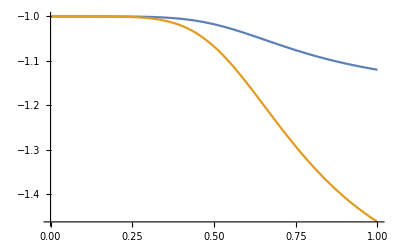

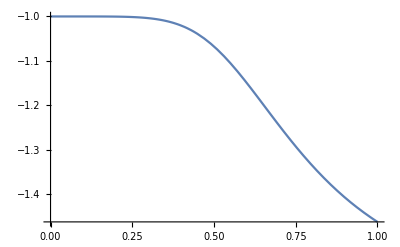

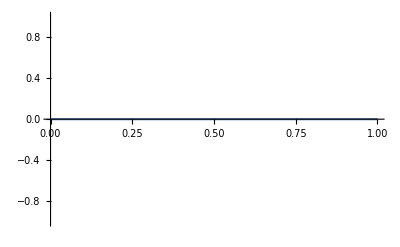

```mathematica
Plot[{Re[OmegaCG1],Re[OmegaCG2]},{a,0,1}]
Plot[Re[OmegaCG2],{a,0,1}]
Plot[Im[OmegaCG1],{a,0,1}]
```

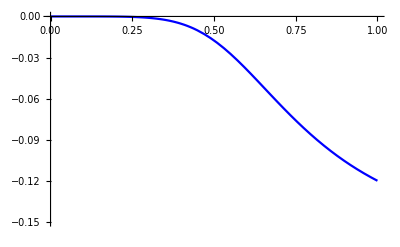

```mathematica
Omegaplot=OmegaCG1+1//Simplify;
OmegaMyPlot=Plot[Omegaplot,{a,0,1},PlotStyle->Blue, PlotRange->{{0,1},{-0.15,0}} ]
```

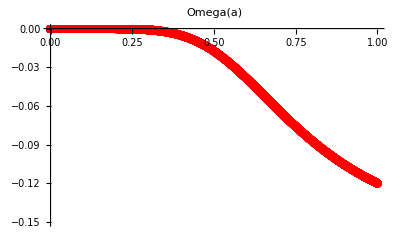

```mathematica
OmegaEFTCAMBPlot=ListPlot[
dataEFTCAMB⟦All,{1,4}⟧
,Joined->False
,PlotMarkers->Automatic, PlotStyle->Red, PlotRange->{{0,1},{-0.15,0}}, PlotLabel->"Omega(a)"
]
```

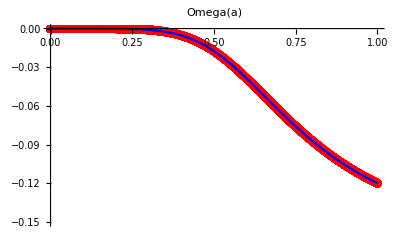

```mathematica
Show[OmegaEFTCAMBPlot,OmegaMyPlot]
```

```mathematica
Omegaprime = -(4 (-1)^(-p (1+1/s)) Subscript[c, 4] p (1+s) Subscript[χ, DS]^(-p (1+1/s)) ℋ[a]^(-1+(2 p (1+s))/s) φ'[a]^(-1+(2 p (1+s))/s) (ℋ[a] φ''[a]+φ'[a] ℋ'[a]))/s;
```

```mathematica
OmegaprimeCG = Omegaprime/.DeSitterFP/.CGSubstitute/.Xds->7.613018601091973 H0^2 M^2/.c4->0.08485200961571562//Simplify;
```

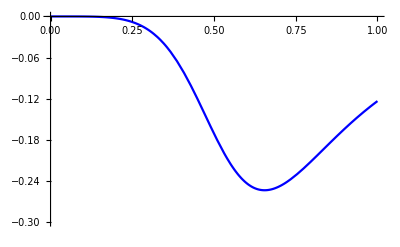

```mathematica
OmegaprimePlot=Plot[OmegaprimeCG,{a,0,1},PlotStyle->Blue, PlotRange->{{0,1},{-0.3,0}}]
```

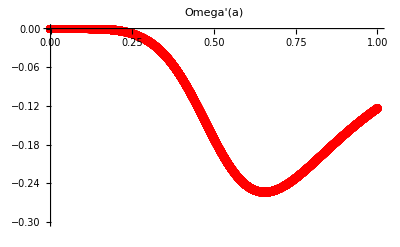

```mathematica
OmegaprimeEFTCAMBPlot=ListPlot[
dataEFTCAMB⟦All,{1,5}⟧
,Joined->False
,PlotMarkers->Automatic, PlotStyle->Red, PlotRange->{{0,1},{-0.3,0}}, PlotLabel->"Omega'(a)"
]
```

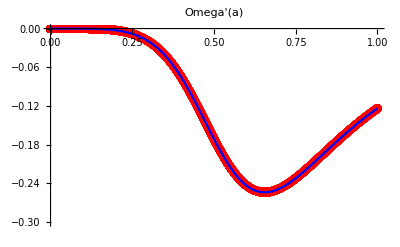

```mathematica
Show[OmegaprimeEFTCAMBPlot,OmegaprimePlot]
```

```mathematica
Omegaprimeprime = -(4 (-1)^(-p (1+1/s)) Subscript[c, 4] p (1+s) Subscript[χ, DS]^(-p (1+1/s)) ℋ[a]^(-2+(2 p (1+s))/s) φ'[a]^(-2+(2 p (1+s))/s) (ℋ[a]^2 ((-s+2 p (1+s)) φ''[a]^2+s φ'[a] φ'''[a])+(-s+2 p (1+s)) φ'[a]^2 ℋ'[a]^2+ℋ[a] φ'[a] (4 p (1+s) φ''[a] ℋ'[a]+s φ'[a] ℋ''[a])))/s^2;
```

```mathematica
OmegaprimeprimeCG = Omegaprimeprime/.DeSitterFP/.CGSubstitute/.Xds->7.613018601091973 H0^2 M^2/.c4->0.08485200961571562//Simplify;
```

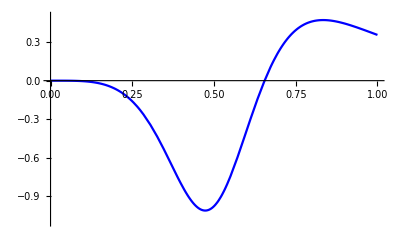

```mathematica
OmegaprimeprimePlot=Plot[OmegaprimeprimeCG,{a,0,1},PlotStyle->Blue, PlotRange->{{0,1},{-1.1,0.5}}]
```

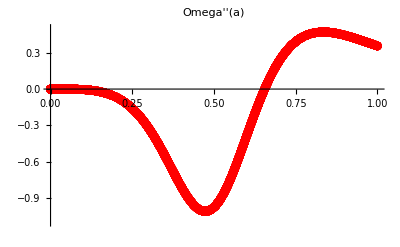

```mathematica
OmegaprimeprimeEFTCAMBPlot=ListPlot[
dataEFTCAMB⟦All,{1,6}⟧
,Joined->False
,PlotMarkers->Automatic, PlotStyle->Red, PlotRange->{{0,1},{-1.1,0.5}}, PlotLabel->"Omega''(a)"
]
```

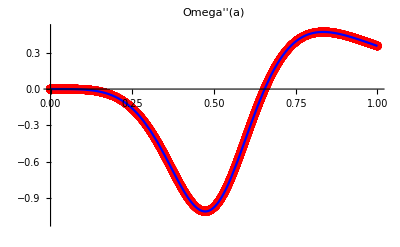

```mathematica
Show[OmegaprimeprimeEFTCAMBPlot,OmegaprimeprimePlot]
```

```mathematica
Omegaprimeprimeprime = -1/s^3 4 (-1)^(-p (1+1/s)) Subscript[c, 4] p (1+s) Subscript[χ, DS]^(-p (1+1/s)) ℋ[a]^(-3+(2 p (1+s))/s) φ'[a]^(-3+(2 p (1+s))/s) (ℋ[a]^3 (2 (s^2-3 p s (1+s)+2 p^2 (1+s)^2) φ''[a]^3+3 s (-s+2 p (1+s)) φ'[a] φ''[a] φ'''[a]+s^2 φ'[a]^2 φ''''[a])+2 (s^2-3 p s (1+s)+2 p^2 (1+s)^2) φ'[a]^3 ℋ'[a]^3+3 (-s+2 p (1+s)) ℋ[a] φ'[a]^2 ℋ'[a] (2 p (1+s) φ''[a] ℋ'[a]+s φ'[a] ℋ''[a])+ℋ[a]^2 φ'[a] (6 p (1+s) (-s+2 p (1+s)) φ''[a]^2 ℋ'[a]+6 p s (1+s) φ'[a] φ''[a] ℋ''[a]+s φ'[a] (6 p (1+s) φ'''[a] ℋ'[a]+s φ'[a] Derivative[3][ℋ][a])));
```

```mathematica
OmegaprimeprimeprimeCG = Omegaprimeprimeprime/.DeSitterFP/.CGSubstitute/.Xds->7.613018601091973 H0^2 M^2/.c4->0.08485200961571562//Simplify;
```

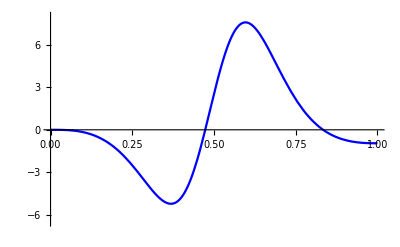

```mathematica
OmegaprimeprimeprimePlot=Plot[OmegaprimeprimeprimeCG,{a,0,1},PlotStyle->Blue, PlotRange->{{0,1},{-6.5,8}}]
```

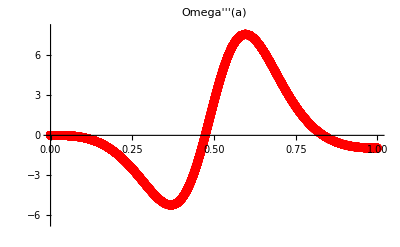

```mathematica
OmegaprimeprimeprimeEFTCAMBPlot=ListPlot[
dataEFTCAMB⟦All,{1,7}⟧
,Joined->False
,PlotMarkers->Automatic, PlotStyle->Red, PlotRange->{{0,1},{-6.5,8}}, PlotLabel->"Omega'''(a)"
]
```

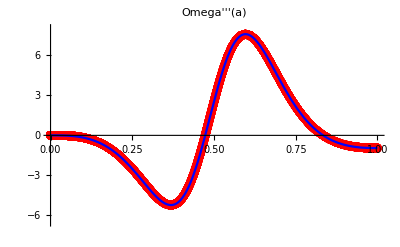

```mathematica
Show[OmegaprimeprimeprimeEFTCAMBPlot,OmegaprimeprimeprimePlot]
```

#### Lambda

```mathematica
LEFT=1/(s^2 φ'[a]^6)(-1)^(-p (2+1/s)) ⅈ^(-p/s) Subscript[χ, DS]^(-p (2+3/(2 s))) ((-1)^(1+p+p/s) ⅈ^(p/s) a^2 Subscript[c, 2] Subscript[H, DS]^2 s^2 Subscript[χ, DS]^(p+(3 p)/(2 s)) ℋ[a]^(2 p) φ'[a]^(6+2 p)-√2 a^2 Subscript[c, 3] ⅇ^((ⅈ p π (1+s))/s) Subscript[H, DS] s (p-s+2 p s) Subscript[χ, DS]^(p (1+1/s)) ℋ[a]^(1+p (2+1/s)) φ'[a]^(5+p (2+1/s)) φ''[a]+4 (-1)^p ⅈ^(p/s) Subscript[χ, DS]^(p+p/(2 s)) ℋ[a]^(2 (1+p+p/s)) φ'[a]^((2 p (1+s))/s) (Subscript[c, 4] p s (1+s) φ'[a]^6+a^2 Subscript[c, 4] p (1+s) (-s+2 p (1+s)) φ'[a]^4 φ''[a]^2+a φ'[a]^5 (4 Subscript[c, 4] p^2 (1+s)^2 φ''[a]+a Subscript[c, 4] p s (1+s) φ'''[a]))-√2 a^2 Subscript[c, 3] ⅇ^((ⅈ p π (1+s))/s) Subscript[H, DS] s (p-s+2 p s) Subscript[χ, DS]^(p (1+1/s)) ℋ[a]^(p (2+1/s)) φ'[a]^(6+p (2+1/s)) ℋ'[a]+8 (-1)^p ⅈ^(p/s) a^2 Subscript[c, 4] p^2 (1+s)^2 Subscript[χ, DS]^(p+p/(2 s)) ℋ[a]^((2 p (1+s))/s) φ'[a]^(6+(2 p (1+s))/s) ℋ'[a]^2+4 (-1)^p ⅈ^(p/s) a Subscript[χ, DS]^(p+p/(2 s)) ℋ[a]^(1+(2 p (1+s))/s) φ'[a]^(5+(2 p (1+s))/s) (a Subscript[c, 4] p (1+s) (s+4 p (1+s)) φ''[a] ℋ'[a]+φ'[a] (2 Subscript[c, 4] p (1+s) (s+2 p (1+s)) ℋ'[a]+a Subscript[c, 4] p s (1+s) ℋ''[a])))
```

1/(s^2 PhiPrime[a]^6)(-1)^(-p (2+1/s)) ⅈ^(-p/s) XDS^(-p (2+3/(2 s))) ((-1)^(1+p+p/s) ⅈ^(p/s) a^2 c2 Hds^2 s^2 XDS^(p+(3 p)/(2 s)) Hconf[a]^(2 p) PhiPrime[a]^(6+2 p)-√2 a^2 c3 ⅇ^((ⅈ p π (1+s))/s) Hds s (p-s+2 p s) XDS^(p (1+1/s)) Hconf[a]^(1+p (2+1/s)) PhiPrime[a]^(5+p (2+1/s)) PhiPrimePrime[a]+4 (-1)^p ⅈ^(p/s) XDS^(p+p/(2 s)) Hconf[a]^(2 (1+p+p/s)) PhiPrime[a]^((2 p (1+s))/s) (c4 p s (1+s) PhiPrime[a]^6+a^2 c4 p (1+s) (-s+2 p (1+s)) PhiPrime[a]^4 PhiPrimePrime[a]^2+a PhiPrime[a]^5 (4 c4 p^2 (1+s)^2 PhiPrimePrime[a]+a c4 p s (1+s) PhiPrimePrimePrime[a]))-√2 a^2 c3 ⅇ^((ⅈ p π (1+s))/s) Hds s (p-s+2 p s) XDS^(p (1+1/s)) Hconf[a]^(p (2+1/s)) PhiPrime[a]^(6+p (2+1/s)) Hconf'[a]+8 (-1)^p ⅈ^(p/s) a^2 c4 p^2 (1+s)^2 XDS^(p+p/(2 s)) Hconf[a]^((2 p (1+s))/s) PhiPrime[a]^(6+(2 p (1+s))/s) Hconf'[a]^2+4 (-1)^p ⅈ^(p/s) a XDS^(p+p/(2 s)) Hconf[a]^(1+(2 p (1+s))/s) PhiPrime[a]^(5+(2 p (1+s))/s) (a c4 p (1+s) (s+4 p (1+s)) PhiPrimePrime[a] Hconf'[a]+PhiPrime[a] (2 c4 p (1+s) (s+2 p (1+s)) Hconf'[a]+a c4 p s (1+s) Hconf''[a])))

```mathematica
LCGeft=LEFT/.DeSitterFP/.CGSubstitute/.Xds->7.613018601091973 H0^2 M^2/.c4->0.08485200961571562//Simplify
```

a H0^2 ((7.81223×10^15 a^5 (-1.3545×10^12-2.38502×10^15 a+(a (1.41536×10^22+4.9844×10^25 a+6.56698×10^27 a^7))/(√(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))-228246. √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))^2)/((6.77249×10^11+2.38502×10^15 a+114123. √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))^3)-(5.21034×10^16 a^5)/(6.77249×10^11+2.38502×10^15 a+114123. √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))-(1.8302×10^34 a^5 (3.82388×10^40+2.69818×10^73 a^15-1.38399×10^75 a^21-3.57264×10^76 a^27-1.15499×10^77 a^33+6.4436×10^33 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8)+a^26 (-3.22384×10^73-7.38028×10^65 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^32 (-4.37291×10^73-1.60191×10^65 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^20 (-1.73366×10^72-6.40089×10^64 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^25 (-9.45351×10^69-4.79214×10^62 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^19 (-8.10775×10^68-7.10265×10^61 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^24 (-9.02949×10^65-7.49012×10^58 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^18 (-1.68828×10^65-2.8592×10^58 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^17 (-1.35425×10^61-4.91905×10^54 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^16 (-7.97587×10^55-3.01442×10^50 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a (1.11001×10^45+1.64355×10^38 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^2 (1.42643×10^49+1.82487×10^42 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^3 (1.06468×10^53+1.15143×10^46 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^9 (1.20601×10^72+3.5224×10^46 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^4 (5.08448×10^56+4.51292×10^49 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^10 (3.77893×10^57+2.41913×10^50 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^5 (1.61037×10^60+1.12434×10^53 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^11 (1.8371×10^61+8.4577×10^53 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^6 (3.3808×10^63+1.73745×10^56 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^12 (5.23402×10^64+1.54708×10^57 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^7 (4.53377×10^66+1.52116×10^59 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^13 (8.67224×10^67+1.32388×10^60 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^8 (3.5215×10^69+5.77073×10^61 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^14 (7.64044×10^70+3.407×10^62 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))))/((3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8)^(3/2) (5.93439×10^6+2.08987×10^10 a+1. √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))^7)+(a^5 (1.63371×10^89+1.24714×10^131 a^23+3.50983×10^131 a^29-7.78733×10^132 a^35-2.46801×10^133 a^41+2.75295×10^82 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8)+a^34 (-7.13538×10^129-1.61342×10^122 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^40 (-9.01046×10^129-8.43526×10^121 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^28 (6.75506×10^128-8.39723×10^120 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^33 (-2.09736×10^126-1.06173×10^119 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^27 (5.09413×10^125-8.30149×10^117 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^32 (-1.98522×10^122-1.67264×10^115 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^26 (1.87512×10^122-2.58298×10^114 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^25 (3.37224×10^118-2.27871×10^110 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a (6.01123×10^93+9.15999×10^86 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^2 (1.00432×10^98+1.36979×10^91 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^3 (1.0057×10^102+1.2123×10^95 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^4 (6.70647×10^105+7.03176×10^98 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^5 (3.12706×10^109+2.79307×10^102 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^11 (9.02184×10^127+3.60486×10^103 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^17 (6.23074×10^129+6.08043×10^103 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^6 (1.04031×10^113+7.69401×10^105 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^24 (2.37594×10^114+8.08826×10^105 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^12 (2.11836×10^114+1.462×10^107 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^18 (8.2452×10^114+4.72094×10^107 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^7 (2.46926×10^116+1.45139×10^109 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^13 (6.93656×10^117+3.78703×10^110 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^19 (4.37242×10^118+1.94576×10^111 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^8 (4.09803×10^119+1.79433×10^112 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^14 (1.51177×10^121+6.11906×10^113 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^20 (1.38709×10^122+4.49203×10^114 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^9 (4.529×10^122+1.31283×10^115 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^15 (2.11473×10^124+5.63962×10^116 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^10 (2.99982×10^125+4.31693×10^117 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^21 (2.63303×10^125+5.51262×10^117 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^16 (1.723×10^127+2.27045×10^119 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^22 (2.77034×10^128+2.81382×10^120 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))))/((3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8)^(3/2) (5.93439×10^6+2.08987×10^10 a+1. √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))^9)+((0.+2.29736×10^-20 ⅈ) a^6 (-3.30216×10^59-3.38598×10^73 a^4-5.57632×10^74 a^10+4.59177×10^75 a^16-5.56446×10^52 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8)+a^3 (-4.32666×10^70-1.62018×10^63 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^8 (-7.86859×10^67-1.89419×10^60 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^2 (-2.04766×10^67-1.61023×10^60 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a (-4.26397×10^63-5.22559×10^56 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))+a^9 (-4.35447×10^71+4.3845×10^48 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))) √(H0^2 M^2))/(√(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8) (5.93439×10^6+2.08987×10^10 a+1. √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))^4 √((6.77249×10^11+2.38502×10^15 a+114123. √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))/a^2) √(-(1. a^4 H0^2 M^2)/(6.77249×10^11+2.38502×10^15 a+114123. √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))))+((0.+2.90861×10^16 ⅈ) (-8.03811×10^18-4.9844×10^25 a^2+3.28349×10^27 a^8-1.3545×10^12 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8)+a (-4.24609×10^22-2.38502×10^15 √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))) √(-(1. a^4 H0^2 M^2)/(6.77249×10^11+2.38502×10^15 a+114123. √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))))/(√(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8) ((6.77249×10^11+2.38502×10^15 a+114123. √(3.52169×10^13+2.48042×10^17 a+4.36757×10^20 a^2+1.43858×10^22 a^8))/a^2)^(3/2) √(H0^2 M^2)))

```mathematica
a=1
LCGeft/.√(-H0^2 M^2)-> ⅈ √(H0^2 M^2)/.√(H0^2 M^2)->-ⅈ √(-H0^2 M^2)
a=.
```

1

(-2.20403+0. ⅈ) H0^2

```mathematica
a=1
LCGeft/(H0^2)/.H0^2 M^2->1
a=.
```

1

-2.20403+0. ⅈ

```mathematica
a=1
LCGeft/.H0^2 M^2->1/.H0^2-> (70.9/(2.99792458*10^5))^2
a=.
```

1

-1.23273×10^-7+0. ⅈ

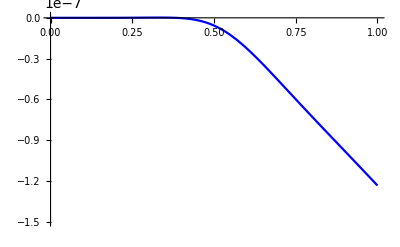

```mathematica
Lplot=LCGeft/.H0^2 M^2->1/.H0^2-> (70.9/(2.99792458*10^5))^2//Simplify;
LambdaMyPlot=Plot[Lplot,{a,0,1},PlotStyle->Blue,PlotRange->{{0,1},{-1.5*10^(-7),10^(-9)}} ]
```

```mathematica
dataEFTCAMB=Import[FileNameJoin[{NotebookDirectory[],"QuarticGalileon_BackgroundEFT.dat"}]]
```

{{1.×10^-10,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00010001,0.,0.,-9.58378×10^-26,-7.1621×10^-21,-4.59973×10^-16,-2.46485×10^-11,2.48833×10^-28,2.11744×10^-29,9.6274×10^-28,8.41109×10^-29},{0.00020002,0.,0.,-1.54089×10^-23,-5.52218×10^-19,-1.68443×10^-14,-4.22713×10^-10,9.42325×10^-27,4.07525×10^-28,3.96389×10^-26,1.80036×10^-27},29995,{1.×10^-10,0.,0.,-1.75374×10^-73,-1.40299×10^-62,-9.82093×10^-52,-5.89256×10^-41,5.04184×10^-64,4.33759×10^-59,1.76464×10^-63,1.51816×10^-58},{1.×10^-10,0.,0.,-1.75374×10^-73,-1.40299×10^-62,-9.82093×10^-52,-5.89256×10^-41,5.04184×10^-64,4.33759×10^-59,1.76464×10^-63,1.51816×10^-58}}
 |  |  |  |

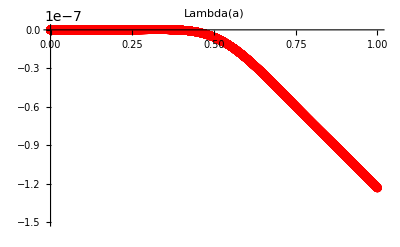

```mathematica
LambdaEFTCAMBPlot=ListPlot[
dataEFTCAMB⟦All,{1,10}⟧
,Joined->False
,PlotMarkers->Automatic, PlotStyle->Red,PlotRange->{{0,1},{-1.5*10^(-7),10^(-9)}} ,PlotLabel->"Lambda(a)"
]
```

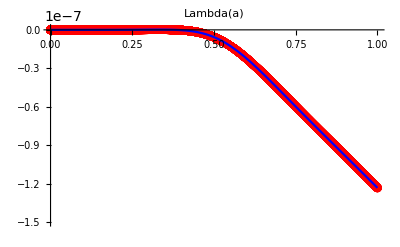

```mathematica
Show[LambdaEFTCAMBPlot,LambdaMyPlot]
```

```mathematica
Lambdadot = 1/(s^3 φ'[a]^7)(-1)^(-p (2+1/s)) ⅈ^(-p/s) Subscript[χ, DS]^(-p (2+3/(2 s))) (-2 a^3 Subscript[c, 2] ⅇ^((ⅈ p π (3+2 s))/(2 s)) Subscript[H, DS]^2 p s^3 Subscript[χ, DS]^(p+(3 p)/(2 s)) ℋ[a]^(1+2 p) φ'[a]^(6+2 p) φ''[a]-√2 a^3 Subscript[c, 3] ⅇ^((ⅈ p π (1+s))/s) Subscript[H, DS] s (p-s+2 p s) Subscript[χ, DS]^(p (1+1/s)) ℋ[a]^(2+p (2+1/s)) φ'[a]^(5+p (2+1/s)) ((p-s+2 p s) φ''[a]^2+s φ'[a] φ'''[a])-2 a^3 Subscript[c, 2] ⅇ^((ⅈ p π (3+2 s))/(2 s)) Subscript[H, DS]^2 p s^3 Subscript[χ, DS]^(p+(3 p)/(2 s)) ℋ[a]^(2 p) φ'[a]^(7+2 p) ℋ'[a]-√2 a^3 Subscript[c, 3] ⅇ^((ⅈ p π (1+s))/s) Subscript[H, DS] p s (1+2 s) (p-s+2 p s) Subscript[χ, DS]^(p (1+1/s)) ℋ[a]^(p (2+1/s)) φ'[a]^(7+p (2+1/s)) ℋ'[a]^2+16 (-1)^p ⅈ^(p/s) a^3 Subscript[c, 4] p^3 (1+s)^3 Subscript[χ, DS]^(p+p/(2 s)) ℋ[a]^((2 p (1+s))/s) φ'[a]^(7+(2 p (1+s))/s) ℋ'[a]^3+4 (-1)^p ⅈ^(p/s) Subscript[χ, DS]^(p+p/(2 s)) ℋ[a]^(3+(2 p (1+s))/s) φ'[a]^((2 p (1+s))/s) (-2 s^2 (-2 Subscript[c, 5] s+Subscript[c, 4] p (1+s)) φ'[a]^7-16 a^2 Subscript[c, 5] s (6 s^2-5 p s (1+s)+p^2 (1+s)^2) φ[a]^5 φ''[a]^2+2 a^3 Subscript[c, 4] p (1+s) (s^2-3 p s (1+s)+2 p^2 (1+s)^2) φ'[a]^4 φ''[a]^3+a^2 (-s+2 p (1+s)) φ'[a]^5 φ''[a] (4 (-4 Subscript[c, 5] s^2+Subscript[c, 4] p^2 (1+s)^2) φ''[a]+3 a Subscript[c, 4] p s (1+s) φ'''[a])+a s φ'[a]^6 (-2 (Subscript[c, 4] p^2 (1+s)^2+2 Subscript[c, 5] s (p-4 s+p s)) φ''[a]+a (4 (-4 Subscript[c, 5] s^2+Subscript[c, 4] p^2 (1+s)^2) φ'''[a]+a Subscript[c, 4] p s (1+s) φ''''[a]))-8 a Subscript[c, 5] s^2 (p-2 s+p s) φ[a]^4 φ'[a] (φ[a] (-φ''[a]+a φ'''[a])+5 a φ''[a] φ'[a]))-√2 a^3 Subscript[c, 3] ⅇ^((ⅈ p π (1+s))/s) Subscript[H, DS] s (p-s+2 p s) Subscript[χ, DS]^(p (1+1/s)) ℋ[a]^(1+p (2+1/s)) φ'[a]^(6+p (2+1/s)) ((s+p (2+4 s)) φ''[a] ℋ'[a]+s φ'[a] ℋ''[a])+4 (-1)^p ⅈ^(p/s) a^2 Subscript[χ, DS]^(p+p/(2 s)) ℋ[a]^(1+(2 p (1+s))/s) φ'[a]^(2 (1+p+p/s)) ℋ'[a] (-8 Subscript[c, 5] s (-2 s^2-3 p s (1+s)+2 p^2 (1+s)^2) φ[a]^5 ℋ'[a]+φ'[a]^4 (a Subscript[c, 4] p (1+s) (s^2+6 p s (1+s)+12 p^2 (1+s)^2) φ''[a] ℋ'[a]+φ'[a] (2 (s+2 p (1+s)) (-10 Subscript[c, 5] s^2+Subscript[c, 4] p (1+s) (s+2 p (1+s))) ℋ'[a]+a Subscript[c, 4] p s (1+s) (s+6 p (1+s)) ℋ''[a])))-4 (-1)^(1+p) ⅈ^(p/s) a Subscript[χ, DS]^(p+p/(2 s)) ℋ[a]^(2 (1+p+p/s)) φ'[a] (3 a^2 Subscript[c, 4] p (1+s) (-s^2+4 p^2 (1+s)^2) φ'[a]^(4+(2 p (1+s))/s) φ''[a]^2 ℋ'[a]-40 a Subscript[c, 5] s^2 (p-2 s+p s) φ[a]^4 φ'[a]^(1+(2 p (1+s))/s) ℋ'[a] φ'[a]-8 Subscript[c, 5] s (p-2 s+p s) φ[a]^5 φ'[a]^((2 p (1+s))/s) (a (-3 s+4 p (1+s)) φ''[a] ℋ'[a]+φ'[a] (-s ℋ'[a]+a s ℋ''[a]))+a φ'[a]^(5+(2 p (1+s))/s) (3 a Subscript[c, 4] p s (1+s) (s+2 p (1+s)) φ'''[a] ℋ'[a]+φ''[a] (4 (Subscript[c, 4] p^2 (1+s)^2 (3 s+4 p (1+s))-2 Subscript[c, 5] s^2 (4 s+9 p (1+s))) ℋ'[a]+a Subscript[c, 4] p s (1+s) (s+6 p (1+s)) ℋ''[a]))-s φ'[a]^(2 (3+p+p/s)) (2 (Subscript[c, 4] p^2 (1+s)^2+2 Subscript[c, 5] s (p-4 s+p s)) ℋ'[a]-a (2 (-10 Subscript[c, 5] s^2+Subscript[c, 4] p (1+s) (s+2 p (1+s))) ℋ''[a]+a Subscript[c, 4] p s (1+s) Derivative[3][ℋ][a]))));
```

```mathematica
LambdadotCG=Lambdadot/.DeSitterFP/.CGSubstitute/.Xds->7.613018601091973 H0^2 M^2/.c4->0.08485200961571562//Simplify;
```

```mathematica
a=1
LambdadotCG/.√(-H0^2 M^2)-> ⅈ √(H0^2 M^2)/.√(H0^2 M^2)->-ⅈ √(-H0^2 M^2)//Simplify
%/.√(-H0^4 M^4)->ⅈ H0^2 M^2
a=.
```

1

((0.+0.186672 ⅈ) H0 √(-H0^4 M^4))/M^2

(-0.186672+0. ⅈ) H0^3

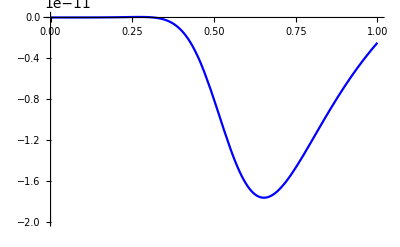

```mathematica
LambdadotCG/.√(-H0^2 M^2)-> ⅈ √(H0^2 M^2)/.√(H0^2 M^2)->-ⅈ √(-H0^2 M^2)//Simplify;
%/.M->1/.H0-> 70.9/(2.99792458*10^5);

plotLambdadot=Plot[%,{a,0,1}, PlotStyle->Blue,PlotRange->{{0,1},{-2*10^(-11),10^(-13)}} ]
```

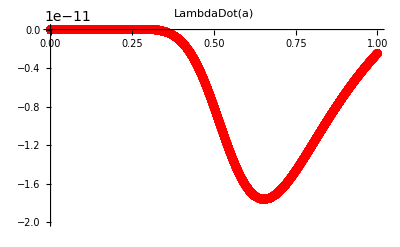

```mathematica
LambdaEFTCAMBPlot=ListPlot[
dataEFTCAMB⟦All,{1,11}⟧
,Joined->False
,PlotMarkers->Automatic, PlotStyle->Red,PlotRange->{{0,1},{-2*10^(-11),10^(-13)}} ,PlotLabel->"LambdaDot(a)"
]
```

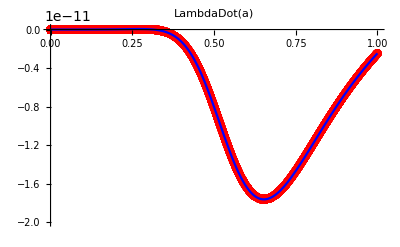

```mathematica
Show[LambdaEFTCAMBPlot,plotLambdadot]
```

c(a)

```mathematica
c=1/(2 s^2 φ'[a]^2)(-1)^(-p (2+1/s)) ⅈ^(-p/s) Subscript[χ, DS]^(-p (2+3/(2 s))) (-2 a^2 Subscript[c, 2] ⅇ^((ⅈ p π (3+2 s))/(2 s)) Subscript[H, DS]^2 p s^2 Subscript[χ, DS]^(p+(3 p)/(2 s)) ℋ[a]^(2 p) φ'[a]^(2+2 p)+√2 a Subscript[c, 3] ⅇ^((ⅈ p π (1+s))/s) Subscript[H, DS] s (p-s+2 p s) Subscript[χ, DS]^(p (1+1/s)) ℋ[a]^(1+p (2+1/s)) φ'[a]^(1+p (2+1/s)) (3 φ'[a]-a φ''[a])-4 (-1)^p ⅈ^(p/s) Subscript[χ, DS]^(p+p/(2 s)) ℋ[a]^(2 (1+p+p/s)) ((-28 Subscript[c, 5] s^2+Subscript[c, 4] p (1+s) (-s+6 p (1+s))) φ'[a]^(2 (1+p+p/s))-a^2 Subscript[c, 4] p (1+s) (-s+2 p (1+s)) φ'[a]^((2 p (1+s))/s) φ''[a]^2-a p (1+s) φ'[a]^(1+(2 p (1+s))/s) ((-3 Subscript[c, 4] s-8 Subscript[c, 5] s+4 Subscript[c, 4] p (1+s)) φ''[a]+a Subscript[c, 4] s φ'''[a]))-√2 a^2 Subscript[c, 3] ⅇ^((ⅈ p π (1+s))/s) Subscript[H, DS] s (p-s+2 p s) Subscript[χ, DS]^(p (1+1/s)) ℋ[a]^(p (2+1/s)) φ'[a]^(2+p (2+1/s)) ℋ'[a]+8 (-1)^p ⅈ^(p/s) a^2 Subscript[c, 4] p^2 (1+s)^2 Subscript[χ, DS]^(p+p/(2 s)) ℋ[a]^((2 p (1+s))/s) φ'[a]^(2 (1+p+p/s)) ℋ'[a]^2+4 (-1)^p ⅈ^(p/s) a Subscript[χ, DS]^(p+p/(2 s)) ℋ[a]^(1+(2 p (1+s))/s) φ'[a]^(1+(2 p (1+s))/s) (a Subscript[c, 4] p (1+s) (s+4 p (1+s)) φ''[a] ℋ'[a]+φ'[a] ((-4 Subscript[c, 5] s (s+2 p (1+s))+Subscript[c, 4] p (1+s) (-s+4 p (1+s))) ℋ'[a]+a Subscript[c, 4] p s (1+s) ℋ''[a])))
```

1/(2 s^2 PhiPrime[a]^2)(-1)^(-p (2+1/s)) ⅈ^(-p/s) XDS^(-p (2+3/(2 s))) (-2 a^2 c2 ⅇ^((ⅈ p π (3+2 s))/(2 s)) Hds^2 p s^2 XDS^(p+(3 p)/(2 s)) Hconf[a]^(2 p) PhiPrime[a]^(2+2 p)+√2 a c3 ⅇ^((ⅈ p π (1+s))/s) Hds s (p-s+2 p s) XDS^(p (1+1/s)) Hconf[a]^(1+p (2+1/s)) PhiPrime[a]^(1+p (2+1/s)) (3 PhiPrime[a]-a PhiPrimePrime[a])-4 (-1)^p ⅈ^(p/s) XDS^(p+p/(2 s)) Hconf[a]^(2 (1+p+p/s)) (c4 p (1+s) (-s+6 p (1+s)) PhiPrime[a]^(2 (1+p+p/s))-a^2 c4 p (1+s) (-s+2 p (1+s)) PhiPrime[a]^((2 p (1+s))/s) PhiPrimePrime[a]^2-a p (1+s) PhiPrime[a]^(1+(2 p (1+s))/s) ((-3 c4 s+4 c4 p (1+s)) PhiPrimePrime[a]+a c4 s PhiPrimePrimePrime[a]))-√2 a^2 c3 ⅇ^((ⅈ p π (1+s))/s) Hds s (p-s+2 p s) XDS^(p (1+1/s)) Hconf[a]^(p (2+1/s)) PhiPrime[a]^(2+p (2+1/s)) Hconf'[a]+8 (-1)^p ⅈ^(p/s) a^2 c4 p^2 (1+s)^2 XDS^(p+p/(2 s)) Hconf[a]^((2 p (1+s))/s) PhiPrime[a]^(2 (1+p+p/s)) Hconf'[a]^2+4 (-1)^p ⅈ^(p/s) a XDS^(p+p/(2 s)) Hconf[a]^(1+(2 p (1+s))/s) PhiPrime[a]^(1+(2 p (1+s))/s) (a c4 p (1+s) (s+4 p (1+s)) PhiPrimePrime[a] Hconf'[a]+PhiPrime[a] (c4 p (1+s) (-s+4 p (1+s)) Hconf'[a]+a c4 p s (1+s) Hconf''[a])))

```mathematica
cCG=c/.DeSitterFP/.CGSubstitute/.Xds->7.613018601091973 H0^2 M^2/.c4->0.08485200961571562//Simplify;
```

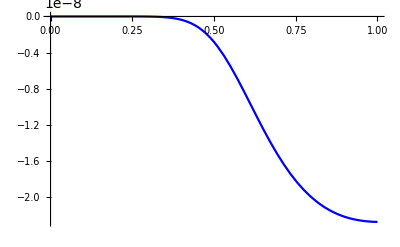

```mathematica
cCG/.H0^2 M^2->1/.H0-> 70.9/(2.99792458 10^5);
plotc=Plot[%,{a,0,1}, PlotStyle->Blue]
```

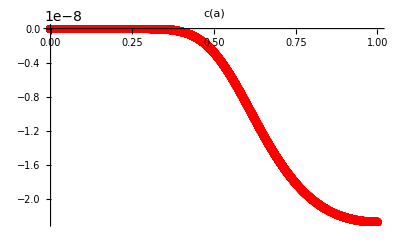

```mathematica
cEFTCAMBPlot=ListPlot[
dataEFTCAMB⟦All,{1,8}⟧
,Joined->False
,PlotMarkers->Automatic, PlotStyle->Red,PlotRange->{{0,1},{0,-2.5*10^-8}}, PlotLabel->"c(a)"
]
```

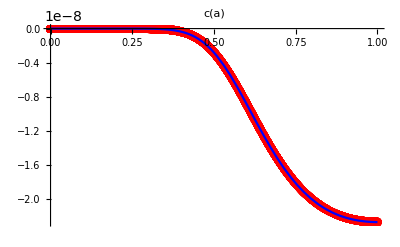

```mathematica
Show[cEFTCAMBPlot,plotc]
```

```mathematica
cdot = 1/(2 s^3 φ'[a]^3)(-1)^(-p (2+1/s)) ⅈ^(-p/s) Subscript[χ, DS]^(-p (2+3/(2 s))) (-4 a^3 Subscript[c, 2] ⅇ^((ⅈ p π (3+2 s))/(2 s)) Subscript[H, DS]^2 p^2 s^3 Subscript[χ, DS]^(p+(3 p)/(2 s)) ℋ[a]^(1+2 p) φ'[a]^(2+2 p) φ''[a]+√2 a Subscript[c, 3] ⅇ^((ⅈ p π (1+s))/s) Subscript[H, DS] s (p-s+2 p s) Subscript[χ, DS]^(p (1+1/s)) ℋ[a]^(2+p (2+1/s)) φ'[a]^(1+p (2+1/s)) (-3 s φ'[a]^2+a^2 (s-p (1+2 s)) φ''[a]^2+a φ'[a] (3 (p+2 p s) φ''[a]-a s φ'''[a]))+4 (-1)^p ⅈ^(p/s) Subscript[χ, DS]^(p+p/(2 s)) ℋ[a]^(3+(2 p (1+s))/s) (2 s (-28 Subscript[c, 5] s^2+Subscript[c, 4] p (1+s) (-s+6 p (1+s))) φ'[a]^(3+(2 p (1+s))/s)+2 a^3 Subscript[c, 4] p (1+s) (s^2-3 p s (1+s)+2 p^2 (1+s)^2) φ'[a]^((2 p (1+s))/s) φ''[a]^3+a^2 p (1+s) (-s+2 p (1+s)) φ'[a]^(1+(2 p (1+s))/s) φ''[a] ((-3 Subscript[c, 4] s-8 Subscript[c, 5] s+4 Subscript[c, 4] p (1+s)) φ''[a]+3 a Subscript[c, 4] s φ'''[a])+a p (1+s) φ'[a]^(2 (1+p+p/s)) (-(-64 Subscript[c, 5] s^2+Subscript[c, 4] (-3 s^2+2 p s (1+s)+12 p^2 (1+s)^2)) φ''[a]+a s ((-3 Subscript[c, 4] s-8 Subscript[c, 5] s+4 Subscript[c, 4] p (1+s)) φ'''[a]+a Subscript[c, 4] s φ''''[a])))-4 a^3 Subscript[c, 2] ⅇ^((ⅈ p π (3+2 s))/(2 s)) Subscript[H, DS]^2 p^2 s^3 Subscript[χ, DS]^(p+(3 p)/(2 s)) ℋ[a]^(2 p) φ'[a]^(3+2 p) ℋ'[a]-√2 a^3 Subscript[c, 3] ⅇ^((ⅈ p π (1+s))/s) Subscript[H, DS] p s (1+2 s) (p-s+2 p s) Subscript[χ, DS]^(p (1+1/s)) ℋ[a]^(p (2+1/s)) φ'[a]^(3+p (2+1/s)) ℋ'[a]^2+16 (-1)^p ⅈ^(p/s) a^3 Subscript[c, 4] p^3 (1+s)^3 Subscript[χ, DS]^(p+p/(2 s)) ℋ[a]^((2 p (1+s))/s) φ'[a]^(3+(2 p (1+s))/s) ℋ'[a]^3-√2 a^2 Subscript[c, 3] ⅇ^((ⅈ p π (1+s))/s) Subscript[H, DS] s (p-s+2 p s) Subscript[χ, DS]^(p (1+1/s)) ℋ[a]^(1+p (2+1/s)) φ'[a]^(2+p (2+1/s)) (a (s+p (2+4 s)) φ''[a] ℋ'[a]+φ'[a] (-3 (p+s+2 p s) ℋ'[a]+a s ℋ''[a]))+4 (-1)^p ⅈ^(p/s) a^2 Subscript[χ, DS]^(p+p/(2 s)) ℋ[a]^(1+(2 p (1+s))/s) φ'[a]^(2 (1+p+p/s)) ℋ'[a] (a Subscript[c, 4] p (1+s) (s^2+6 p s (1+s)+12 p^2 (1+s)^2) φ''[a] ℋ'[a]+φ'[a] ((s+2 p (1+s)) (-4 Subscript[c, 5] s (s+2 p (1+s))+Subscript[c, 4] p (1+s) (-s+4 p (1+s))) ℋ'[a]+a Subscript[c, 4] p s (1+s) (s+6 p (1+s)) ℋ''[a]))+4 (-1)^p ⅈ^(p/s) a Subscript[χ, DS]^(p+p/(2 s)) ℋ[a]^(2 (1+p+p/s)) φ'[a] (3 a^2 Subscript[c, 4] p (1+s) (-s^2+4 p^2 (1+s)^2) φ'[a]^((2 p (1+s))/s) φ''[a]^2 ℋ'[a]+a p (1+s) φ'[a]^(1+(2 p (1+s))/s) (3 a Subscript[c, 4] s (s+2 p (1+s)) φ'''[a] ℋ'[a]+φ''[a] (2 (-4 Subscript[c, 5] s (3 s+4 p (1+s))+Subscript[c, 4] (-3 s^2+8 p^2 (1+s)^2)) ℋ'[a]+a Subscript[c, 4] s (s+6 p (1+s)) ℋ''[a]))-φ'[a]^(2 (1+p+p/s)) ((-4 Subscript[c, 5] s^2 (15 s+16 p (1+s))+Subscript[c, 4] p (1+s) (-3 s^2+14 p s (1+s)+12 p^2 (1+s)^2)) ℋ'[a]+a s ((4 Subscript[c, 5] s (s+2 p (1+s))-Subscript[c, 4] p (1+s) (-s+4 p (1+s))) ℋ''[a]-a Subscript[c, 4] p s (1+s) Derivative[3][ℋ][a]))));
```

```mathematica
cdotCG=cdot/.DeSitterFP/.CGSubstitute/.Xds->7.613018601091973 H0^2 M^2/.c4->0.08485200961571562//Simplify;
```

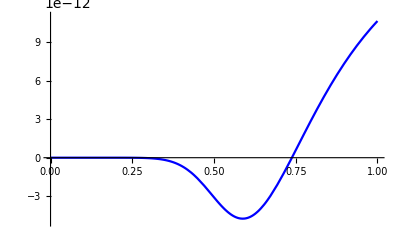

```mathematica
cdotCG/.H0^2 M^2->1/.H0-> 70.9/(2.99792458 10^5);
plotcdot=Plot[%,{a,0,1}, PlotStyle->Blue,PlotRange->{{0,1},{-5 10^(-12),1.1*10^-11}}]
```

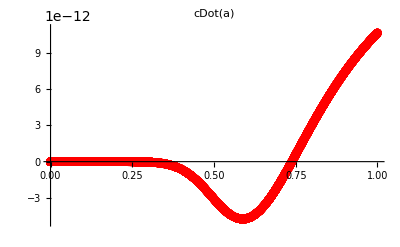

```mathematica
cDotEFTCAMBPlot=ListPlot[
dataEFTCAMB⟦All,{1,9}⟧
,Joined->False
,PlotMarkers->Automatic, PlotStyle->Red,PlotRange->{{0,1},{-5 10^(-12),1.1*10^-11}}, PlotLabel->"cDot(a)"
]
```

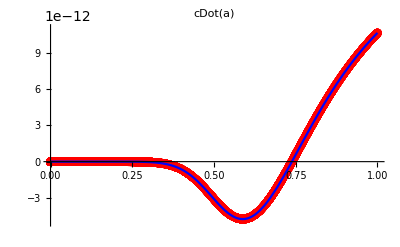

```mathematica
Show[cDotEFTCAMBPlot,plotcdot]
```

Gamma 1

```mathematica
gamma1 = 1/(4 a^2 Subscript[H, 0]^2 s^3)(-4 (-1)^-p a^2 Subscript[c, 2] Subscript[H, DS]^2 (-1+p) p s^3 Subscript[χ, DS]^-p ℋ[a]^(2 p) φ'[a]^(2 p)+(-1)^-p ⅈ^(-p/s) √2 a Subscript[c, 3] Subscript[H, DS] s (p-s+2 p s) Subscript[χ, DS]^(-(p+2 p s)/(2 s)) ℋ[a]^(p (2+1/s)) φ'[a]^(-1+p (2+1/s)) (ℋ[a] (3 (p-2 s+2 p s) φ'[a]+a s φ''[a])+a s φ'[a] ℋ'[a])+16 (-1)^(-p (1+1/s)) Subscript[c, 5] s^2 Subscript[χ, DS]^(-p (1+1/s)) ℋ[a]^(1+(2 p (1+s))/s) φ'[a]^(-1+(2 p (1+s))/s) (2 a (p-2 s+p s) φ''[a]+s ℋ[a] (11 φ'[a]+4 a φ''[a])+a (s+2 p (1+s)) φ'[a] ℋ'[a])-4 (-1)^(-p (1+1/s)) Subscript[c, 4] p (1+s) Subscript[χ, DS]^(-p (1+1/s)) ℋ[a]^((2 p (1+s))/s) φ'[a]^(-2+(2 p (1+s))/s) (ℋ[a]^2 (2 (2 s^2-9 p s (1+s)+6 p^2 (1+s)^2) φ'[a]^2+a^2 s (-s+2 p (1+s)) φ''[a]^2+a s φ'[a] ((-3 s+4 p (1+s)) φ''[a]+a s φ'''[a]))+2 a^2 p s (1+s) φ'[a]^2 ℋ'[a]^2+a s ℋ[a] φ'[a] (a (s+4 p (1+s)) φ''[a] ℋ'[a]+φ'[a] ((-s+4 p (1+s)) ℋ'[a]+a s ℋ''[a]))));
```

```mathematica
gamma1CG=gamma1/.DeSitterFP/.CGSubstitute/.Xds->7.613018601091973 H0^2 M^2/.c4->0.08485200961571562//Simplify;
```

```mathematica
a=1
gamma1CG/.H0^2 M^2-> 1
a=.
```

1

0.724023+0. ⅈ

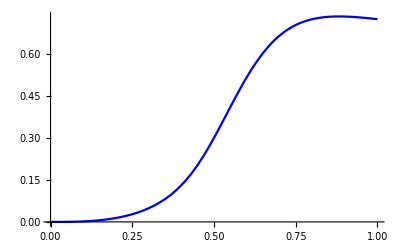

```mathematica
gamma1CG/.H0^2 M^2-> 1;
gamma1plot=Plot[%,{a,0,1},PlotStyle->Blue]
```

```mathematica
dataEFTCAMB2ndOrder=Import[FileNameJoin[{NotebookDirectory[],"QuarticGalileon_SecondOrdEFT.dat"}]]
```

{{1.×10^-10,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.00010001,0.,0.,2.42776×10^-13,9.82309×10^-9,1.71418×10^-19,9.21737×10^-15,3.83351×10^-25,2.86484×10^-20,-3.83351×10^-25,-2.86484×10^-20,-1.83989×10^-15,1.91676×10^-25,1.43242×10^-20,0.,0.},29996,{1.×10^-10,0.,0.,1.78632×10^-37,7.14527×10^-27,3.53239×10^-55,2.11943×10^-44,7.01496×10^-73,5.61196×10^-62,-7.01496×10^-73,-5.61196×10^-62,-3.92837×10^-51,3.50748×10^-73,2.80598×10^-62,0.,0.},{1.×10^-10,0.,0.,1.78632×10^-37,7.14527×10^-27,3.53239×10^-55,2.11943×10^-44,7.01496×10^-73,5.61196×10^-62,-7.01496×10^-73,-5.61196×10^-62,-3.92837×10^-51,3.50748×10^-73,2.80598×10^-62,0.,0.}}
 |  |  |  |

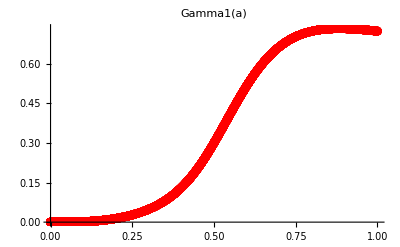

```mathematica
gamma1EFTCAMBPlot=ListPlot[
dataEFTCAMB2ndOrder⟦All,{1,4}⟧
,Joined->False
,PlotMarkers->Automatic, PlotStyle->Red, PlotLabel->"Gamma1(a)"
]
```

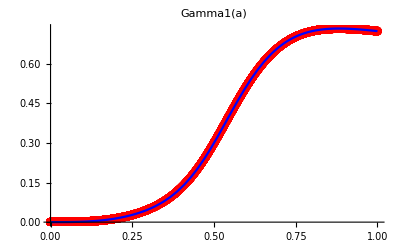

```mathematica
Show[gamma1EFTCAMBPlot,gamma1plot]
```

```mathematica
gamma1prime = 1/(4 a^3 Subscript[H, 0]^2 s^4 ℋ[a] φ'[a]^3)(-1)^(-p (2+1/s)) ⅈ^(-p/s) Subscript[χ, DS]^(-p (2+3/(2 s))) (-8 a^3 Subscript[c, 2] ⅇ^((ⅈ p π (3+2 s))/(2 s)) Subscript[H, DS]^2 (-1+p) p^2 s^4 Subscript[χ, DS]^(p+(3 p)/(2 s)) ℋ[a]^(1+2 p) φ'[a]^(2+2 p) φ''[a]+√2 a Subscript[c, 3] Subscript[H, DS] s Subscript[χ, DS]^(p (1+1/s)) ℋ[a]^(2+p (2+1/s)) φ'[a]^(1+p (2+1/s)) (-3 (-1)^(p (1+1/s)) s (2 s^2-3 p s (1+2 s)+(p+2 p s)^2) φ'[a]^2+(-1)^(p (1+1/s)) a^2 s (p-s+2 p s)^2 φ''[a]^2+a ⅇ^((ⅈ p π (1+s))/s) (p-s+2 p s) φ'[a] (3 p (1+2 s) (p-2 s+2 p s) φ''[a]+a s^2 φ'''[a]))+4 (-1)^p ⅈ^(p/s) Subscript[χ, DS]^(p+p/(2 s)) ℋ[a]^(3+(2 p (1+s))/s) (4 s (-22 Subscript[c, 5] s^3+Subscript[c, 4] p (1+s) (2 s^2-9 p s (1+s)+6 p^2 (1+s)^2)) φ'[a]^(3+(2 p (1+s))/s)-2 a^3 Subscript[c, 4] p s (1+s) (s^2-3 p s (1+s)+2 p^2 (1+s)^2) φ'[a]^((2 p (1+s))/s) φ''[a]^3-a^2 s (-s+2 p (1+s)) φ'[a]^(1+(2 p (1+s))/s) φ''[a] ((-16 Subscript[c, 5] s^2+Subscript[c, 4] p (1+s) (-3 s+4 p (1+s))) φ''[a]+3 a Subscript[c, 4] p s (1+s) φ'''[a])-a φ'[a]^(2 (1+p+p/s)) ((-8 Subscript[c, 5] s^3 (-2 s+11 p (1+s))+Subscript[c, 4] p (1+s) (3 s^3+4 p s^2 (1+s)-36 p^2 s (1+s)^2+24 p^3 (1+s)^3)) φ''[a]+a s^2 ((-16 Subscript[c, 5] s^2+Subscript[c, 4] p (1+s) (-3 s+4 p (1+s))) φ'''[a]+a Subscript[c, 4] p s (1+s) φ''''[a])))-8 a^3 Subscript[c, 2] ⅇ^((ⅈ p π (3+2 s))/(2 s)) Subscript[H, DS]^2 (-1+p) p^2 s^4 Subscript[χ, DS]^(p+(3 p)/(2 s)) ℋ[a]^(2 p) φ'[a]^(3+2 p) ℋ'[a]+√2 a^3 Subscript[c, 3] ⅇ^((ⅈ p π (1+s))/s) Subscript[H, DS] p s^2 (1+2 s) (p-s+2 p s) Subscript[χ, DS]^(p (1+1/s)) ℋ[a]^(p (2+1/s)) φ'[a]^(3+p (2+1/s)) ℋ'[a]^2-16 (-1)^p ⅈ^(p/s) a^3 Subscript[c, 4] p^3 s (1+s)^3 Subscript[χ, DS]^(p+p/(2 s)) ℋ[a]^((2 p (1+s))/s) φ'[a]^(3+(2 p (1+s))/s) ℋ'[a]^3+√2 a^2 Subscript[c, 3] ⅇ^((ⅈ p π (1+s))/s) Subscript[H, DS] s (p-s+2 p s) Subscript[χ, DS]^(p (1+1/s)) ℋ[a]^(1+p (2+1/s)) φ'[a]^(2+p (2+1/s)) (a s (s+p (2+4 s)) φ''[a] ℋ'[a]+φ'[a] (3 (-2 s^2-p s (1+2 s)+(p+2 p s)^2) ℋ'[a]+a s^2 ℋ''[a]))-4 (-1)^p ⅈ^(p/s) a^2 s Subscript[χ, DS]^(p+p/(2 s)) ℋ[a]^(1+(2 p (1+s))/s) φ'[a]^(2 (1+p+p/s)) ℋ'[a] (φ''[a] (-8 Subscript[c, 5] s (-2 s^2-3 p s (1+s)+2 p^2 (1+s)^2)+a Subscript[c, 4] p (1+s) (s^2+6 p s (1+s)+12 p^2 (1+s)^2) ℋ'[a])+φ'[a] ((s+2 p (1+s)) (-4 Subscript[c, 5] s (s+2 p (1+s))+Subscript[c, 4] p (1+s) (-s+4 p (1+s))) ℋ'[a]+a Subscript[c, 4] p s (1+s) (s+6 p (1+s)) ℋ''[a]))-4 (-1)^p ⅈ^(p/s) a Subscript[χ, DS]^(p+p/(2 s)) ℋ[a]^(2 (1+p+p/s)) φ'[a] (a s (-s+2 p (1+s)) φ'[a]^((2 p (1+s))/s) φ''[a]^2 (-8 Subscript[c, 5] s (p-2 s+p s)+3 a Subscript[c, 4] p (1+s) (s+2 p (1+s)) ℋ'[a])+s φ'[a]^(1+(2 p (1+s))/s) (a s φ'''[a] (-8 Subscript[c, 5] s (p-2 s+p s)+3 a Subscript[c, 4] p (1+s) (s+2 p (1+s)) ℋ'[a])+φ''[a] (2 a (-4 Subscript[c, 5] s (4 s^2+5 p s (1+s)+2 p^2 (1+s)^2)+Subscript[c, 4] p (1+s) (-3 s^2+8 p^2 (1+s)^2)) ℋ'[a]+s (8 Subscript[c, 5] s (p-2 s+p s)+a^2 Subscript[c, 4] p (1+s) (s+6 p (1+s)) ℋ''[a])))+φ'[a]^(2 (1+p+p/s)) ((-4 Subscript[c, 5] s^3 (21 s+20 p (1+s))+Subscript[c, 4] p (1+s) (9 s^3-32 p s^2 (1+s)-12 p^2 s (1+s)^2+24 p^3 (1+s)^3)) ℋ'[a]+a s^2 ((-4 Subscript[c, 5] s (s+2 p (1+s))+Subscript[c, 4] p (1+s) (-s+4 p (1+s))) ℋ''[a]+a Subscript[c, 4] p s (1+s) Derivative[3][ℋ][a]))));
```

```mathematica
gamma1primeCG = gamma1prime/.DeSitterFP/.CGSubstitute/.Xds->7.613018601091973 H0^2 M^2/.c4->0.08485200961571562;
```

```mathematica
a=1
gamma1primeCG//Simplify//Expand
%/.√(-H0^4 M^4)->ⅈ H0^2 M^2
gamma1primeCG/.H0->1/.M->1//Simplify//Expand
a=.
```

1

-0.963241-((0.+0.829096 ⅈ) √(-H0^4 M^4))/(H0^2 M^2)

-0.134145+0. ⅈ

-0.134145+0. ⅈ

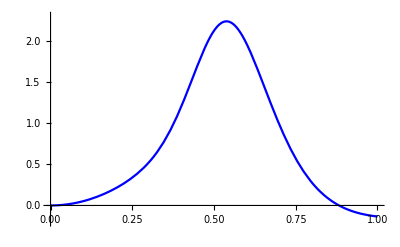

```mathematica
gamma1primeCG/.H0->1/.M->1;
gamma1primeCGplot=Plot[%,{a,0,1},PlotStyle->Blue,PlotRange->{{0,1},{-0.2,2.3}}]
```

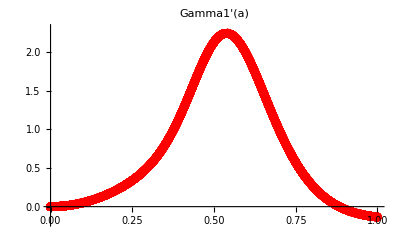

```mathematica
gamma1primeEFTCAMBPlot=ListPlot[
dataEFTCAMB2ndOrder⟦All,{1,5}⟧
,Joined->False
,PlotMarkers->Automatic, PlotStyle->Red,PlotRange->{{0,1},{-0.2,2.3}}, PlotLabel->"Gamma1'(a)"
]
```

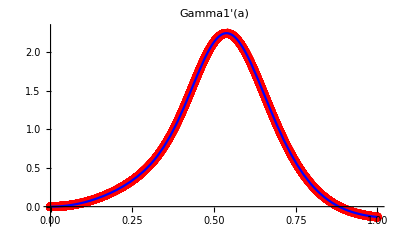

```mathematica
Show[gamma1primeEFTCAMBPlot,gamma1primeCGplot]
```

#### gamma2

```mathematica
gamma2 = 1/(a Subscript[H, 0] s^2 φ'[a])(-1)^(-p (2+1/s)) ⅈ^(-p/s) Subscript[χ, DS]^(-p (2+3/(2 s))) (-√2 a Subscript[c, 3] ⅇ^((ⅈ p π (1+s))/s) Subscript[H, DS] s (p-s+2 p s) Subscript[χ, DS]^(p (1+1/s)) ℋ[a]^(p (2+1/s)) φ'[a]^(1+p (2+1/s))+4 (-1)^p ⅈ^(p/s) Subscript[χ, DS]^(p+p/(2 s)) ℋ[a]^(1+(2 p (1+s))/s) φ'[a]^((2 p (1+s))/s) (2 (-8 Subscript[c, 5] s^2+Subscript[c, 4] p (1+s) (-s+2 p (1+s))) φ'[a]+a Subscript[c, 4] p s (1+s) φ''[a])+4 (-1)^p ⅈ^(p/s) a Subscript[c, 4] p s (1+s) Subscript[χ, DS]^(p+p/(2 s)) ℋ[a]^((2 p (1+s))/s) φ'[a]^(1+(2 p (1+s))/s) ℋ'[a]);
```

```mathematica
gamma2/.p->1/.s->1;
Coefficient[%,c4]//Expand
```

(48 Hconf[a]^5 PhiPrime[a]^4)/(a H0 XDS^2)+(8 Hconf[a]^5 PhiPrime[a]^3 PhiPrimePrime[a])/(H0 XDS^2)+(8 Hconf[a]^4 PhiPrime[a]^4 Hconf'[a])/(H0 XDS^2)

```mathematica
gamma2CG=gamma2/.DeSitterFP/.CGSubstitute/.Xds->7.613018601091973 H0^2 M^2/.c4->0.08485200961571562//Simplify;
```

```mathematica
a=1
gamma2CG/.Subscript[H, 0]^2 M^2->1
a=.
```

1

-0.57043+0. ⅈ

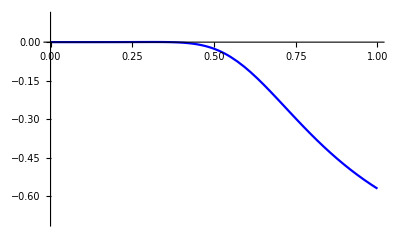

```mathematica
gamma2CG/.H0^2 M^2-> 1;
gamma2plot=Plot[%,{a,0,1},PlotStyle->Blue,PlotRange->{{0,1},{-0.7,0.1}}]
```

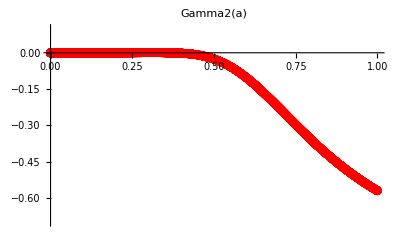

```mathematica
gamma2EFTCAMBPlot=ListPlot[
dataEFTCAMB2ndOrder⟦All,{1,6}⟧
,Joined->False
,PlotMarkers->Automatic, PlotStyle->Red,PlotRange->{{0,1},{-0.7,0.1}}, PlotLabel->"Gamma2(a)"
]
```

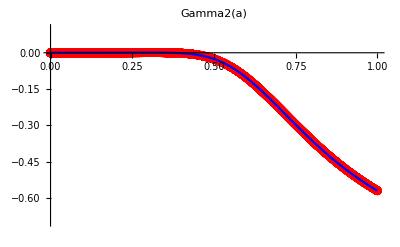

```mathematica
Show[gamma2EFTCAMBPlot,gamma2plot]
```

```mathematica
gamma2prime = 1/(a^2 Subscript[H, 0] s^3 ℋ[a] φ'[a]^2)(-1)^(-p (2+1/s)) ⅈ^(-p/s) Subscript[χ, DS]^(-p (2+3/(2 s))) (-√2 a^2 Subscript[c, 3] ⅇ^((ⅈ p π (1+s))/s) Subscript[H, DS] p s (1+2 s) (p-s+2 p s) Subscript[χ, DS]^(p (1+1/s)) ℋ[a]^(1+p (2+1/s)) φ'[a]^(1+p (2+1/s)) φ''[a]-4 (-1)^p ⅈ^(p/s) Subscript[χ, DS]^(p+p/(2 s)) ℋ[a]^(2 (1+p+p/s)) (2 s (-8 Subscript[c, 5] s^2+Subscript[c, 4] p (1+s) (-s+2 p (1+s))) φ'[a]^(2 (1+p+p/s))-a^2 Subscript[c, 4] p s (1+s) (-s+2 p (1+s)) φ'[a]^((2 p (1+s))/s) φ''[a]^2-a p (1+s) φ'[a]^(1+(2 p (1+s))/s) (4 (-8 Subscript[c, 5] s^2+Subscript[c, 4] p (1+s) (-s+2 p (1+s))) φ''[a]+a Subscript[c, 4] s^2 φ'''[a]))-√2 a^2 Subscript[c, 3] ⅇ^((ⅈ p π (1+s))/s) Subscript[H, DS] p s (1+2 s) (p-s+2 p s) Subscript[χ, DS]^(p (1+1/s)) ℋ[a]^(p (2+1/s)) φ'[a]^(2+p (2+1/s)) ℋ'[a]+8 (-1)^p ⅈ^(p/s) a^2 Subscript[c, 4] p^2 s (1+s)^2 Subscript[χ, DS]^(p+p/(2 s)) ℋ[a]^((2 p (1+s))/s) φ'[a]^(2 (1+p+p/s)) ℋ'[a]^2+4 (-1)^p ⅈ^(p/s) a Subscript[χ, DS]^(p+p/(2 s)) ℋ[a]^(1+(2 p (1+s))/s) φ'[a]^(1+(2 p (1+s))/s) (a Subscript[c, 4] p s (1+s) (s+4 p (1+s)) φ''[a] ℋ'[a]+φ'[a] (2 (s+2 p (1+s)) (-8 Subscript[c, 5] s^2+Subscript[c, 4] p (1+s) (-s+2 p (1+s))) ℋ'[a]+a Subscript[c, 4] p s^2 (1+s) ℋ''[a])));
```

```mathematica
gamma2primeCG=gamma2prime/.DeSitterFP/.CGSubstitute/.Xds->7.613018601091973 H0^2 M^2/.c4->0.08485200961571562;
```

```mathematica
a=1
gamma2primeCG//Expand
a=.
```

1

(1.96045+0. ⅈ)+((0.+2.76117 ⅈ) √(-H0^2 M^2) √(H0^2 M^2))/(H0^2 M^2)

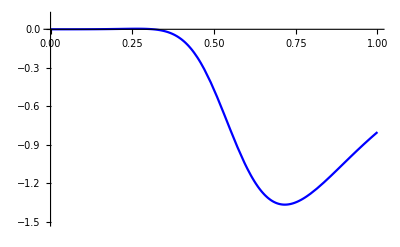

```mathematica
gamma2primeCG//Expand;
%/.H0->1/.M->1;
gamma2primeplot=Plot[%,{a,0,1},PlotStyle->Blue,PlotRange->{{0,1},{-1.5,0.1}}]
```

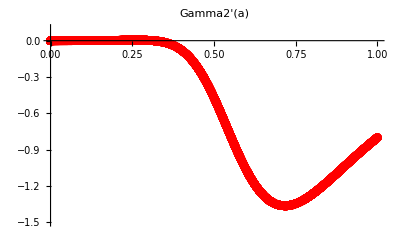

```mathematica
gamma2primeEFTCAMBPlot=ListPlot[
dataEFTCAMB2ndOrder⟦All,{1,7}⟧
,Joined->False
,PlotMarkers->Automatic, PlotStyle->Red,PlotRange->{{0,1},{-1.5,0.1}}, PlotLabel->"Gamma2'(a)"
]
```

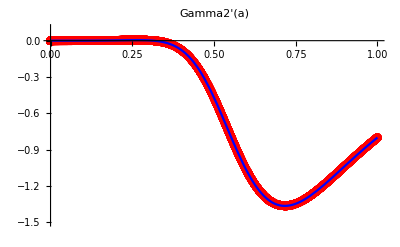

```mathematica
Show[gamma2primeEFTCAMBPlot,gamma2primeplot]
```

#### gamma 3

```mathematica
gamma3 = (4 (-1)^(-p (1+1/s)) (-2 Subscript[c, 5] s+Subscript[c, 4] p (1+s)) Subscript[χ, DS]^(-p (1+1/s)) ℋ[a]^((2 p (1+s))/s) φ'[a]^((2 p (1+s))/s))/s;
```

```mathematica
gamma3CG=gamma3/.DeSitterFP/.CGSubstitute/.Xds->7.613018601091973 H0^2 M^2/.c4->0.08485200961571562//Simplify;
```

```mathematica
a=1
gamma3CG
a=.
```

1

0.479866

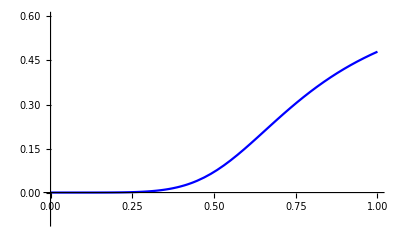

```mathematica
gamma3plot=Plot[gamma3CG,{a,0,1},PlotStyle->Blue,PlotRange->{{0,1},{-0.1,0.6}}]
```

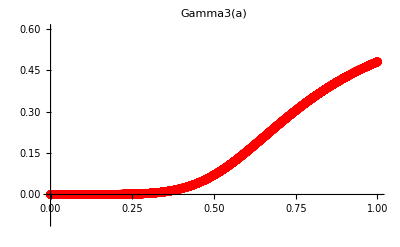

```mathematica
gamma3EFTCAMBPlot=ListPlot[
dataEFTCAMB2ndOrder⟦All,{1,8}⟧
,Joined->False
,PlotMarkers->Automatic, PlotStyle->Red,PlotRange->{{0,1},{-0.1,0.6}}, PlotLabel->"Gamma3(a)"
]
```

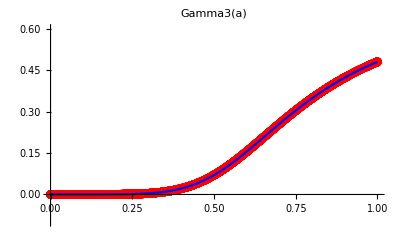

```mathematica
Show[gamma3EFTCAMBPlot,gamma3plot]
```

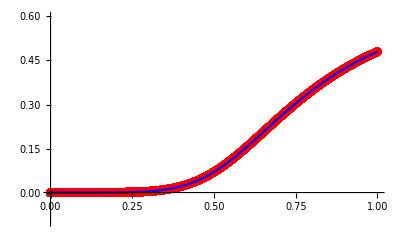

```mathematica
gamma3prime = (8 (-1)^(-p (1+1/s)) p (1+s) (-2 Subscript[c, 5] s+Subscript[c, 4] p (1+s)) Subscript[χ, DS]^(-p (1+1/s)) ℋ[a]^(-1+(2 p (1+s))/s) φ'[a]^(-1+(2 p (1+s))/s) (ℋ[a] φ''[a]+φ'[a] ℋ'[a]))/s^2;
```

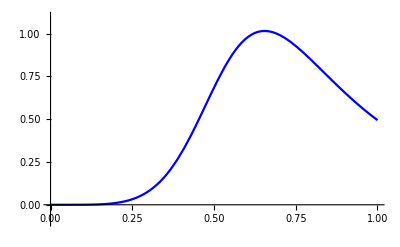

```mathematica
gamma3primeCG=gamma3prime/.DeSitterFP/.CGSubstitute/.Xds->7.613018601091973 H0^2 M^2/.c4->0.08485200961571562//Simplify;
gamma3primeplot=Plot[gamma3primeCG,{a,0,1},PlotStyle->Blue,PlotRange->{{0,1},{-0.1,1.1}}]
```

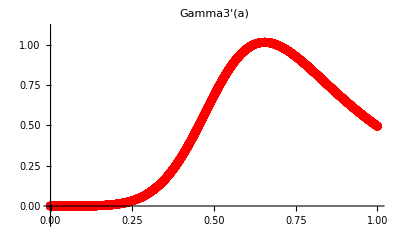

```mathematica
gamma3primeEFTCAMBPlot=ListPlot[
dataEFTCAMB2ndOrder⟦All,{1,9}⟧
,Joined->False
,PlotMarkers->Automatic, PlotStyle->Red,PlotRange->{{0,1},{-0.1,1.1}}, PlotLabel->"Gamma3'(a)"
]
```

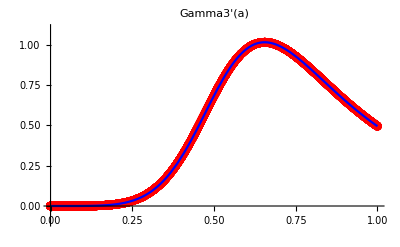

```mathematica
Show[gamma3primeEFTCAMBPlot,gamma3primeplot]
```

#### gamma 4

```mathematica
gamma4 = -(4 (-1)^(-p (1+1/s)) (-2 Subscript[c, 5] s+Subscript[c, 4] p (1+s)) Subscript[χ, DS]^(-p (1+1/s)) ℋ[a]^((2 p (1+s))/s) φ'[a]^((2 p (1+s))/s))/s;
```

```mathematica
gamma4CG=gamma4/.DeSitterFP/.CGSubstitute/.Xds->7.613018601091973 H0^2 M^2/.c4->0.08485200961571562//Simplify;
```

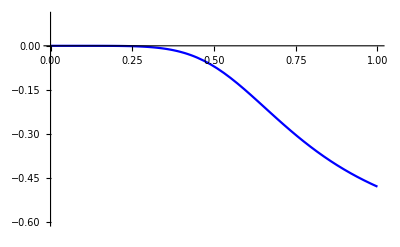

```mathematica
gamma4plot=Plot[gamma4CG,{a,0,1},PlotStyle->Blue,PlotRange->{{0,1},{-0.6,0.1}}]
```

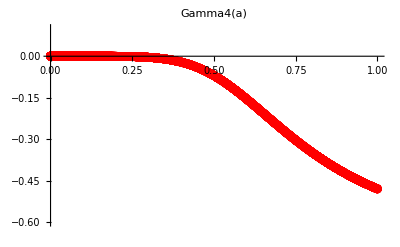

```mathematica
gamma4EFTCAMBPlot=ListPlot[
dataEFTCAMB2ndOrder⟦All,{1,10}⟧
,Joined->False
,PlotMarkers->Automatic, PlotStyle->Red,PlotRange->{{0,1},{-0.6,0.1}}, PlotLabel->"Gamma4(a)"
]
```

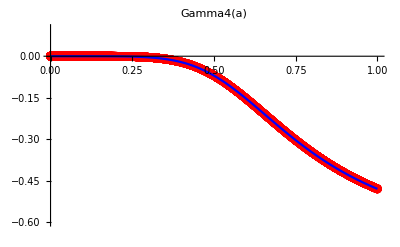

```mathematica
Show[gamma4EFTCAMBPlot,gamma4plot]
```

```mathematica
gamma4prime = -(8 (-1)^(-p (1+1/s)) p (1+s) (-2 Subscript[c, 5] s+Subscript[c, 4] p (1+s)) Subscript[χ, DS]^(-p (1+1/s)) ℋ[a]^(-1+(2 p (1+s))/s) φ'[a]^(-1+(2 p (1+s))/s) (ℋ[a] φ''[a]+φ'[a] ℋ'[a]))/s^2;
```

```mathematica
gamma4primeCG=gamma4prime/.DeSitterFP/.CGSubstitute/.Xds->7.613018601091973 H0^2 M^2/.c4->0.08485200961571562//Simplify;
```

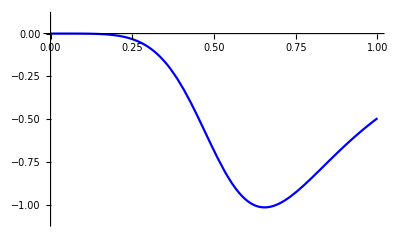

```mathematica
gamma4primeplot=Plot[gamma4primeCG,{a,0,1},PlotStyle->Blue,PlotRange->{{0,1},{-1.1,0.1}}]
```

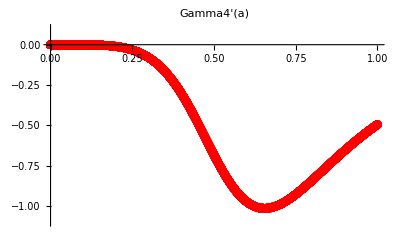

```mathematica
gamma4primeEFTCAMBPlot=ListPlot[
dataEFTCAMB2ndOrder⟦All,{1,11}⟧
,Joined->False
,PlotMarkers->Automatic, PlotStyle->Red,PlotRange->{{0,1},{-1.1,0.1}}, PlotLabel->"Gamma4'(a)"
]
```

```mathematica
Show[gamma4primeEFTCAMBPlot,gamma4primeplot]
```

-Graphics-

```mathematica
gamma4primeprime = -(8 (-1)^(-p (1+1/s)) p (1+s) (-2 Subscript[c, 5] s+Subscript[c, 4] p (1+s)) Subscript[χ, DS]^(-p (1+1/s)) ℋ[a]^(-2+(2 p (1+s))/s) φ'[a]^(-2+(2 p (1+s))/s) (ℋ[a]^2 ((-s+2 p (1+s)) φ''[a]^2+s φ'[a] φ'''[a])+(-s+2 p (1+s)) φ'[a]^2 ℋ'[a]^2+ℋ[a] φ'[a] (4 p (1+s) φ''[a] ℋ'[a]+s φ'[a] ℋ''[a])))/s^3;
```

```mathematica
gamma4primeprimeCG=gamma4primeprime/.DeSitterFP/.CGSubstitute/.Xds->7.613018601091973 H0^2 M^2/.c4->0.08485200961571562//Simplify;
```

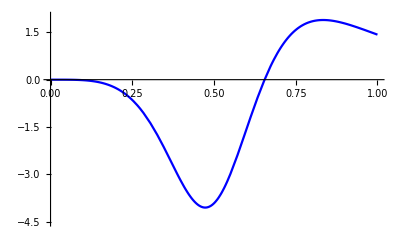

```mathematica
gamma4primeprimeplot=Plot[gamma4primeprimeCG,{a,0,1},PlotStyle->Blue,PlotRange->{{0,1},{-4.5,2}}]
```

```mathematica
gamma4primeprimeEFTCAMBPlot=ListPlot[
dataEFTCAMB2ndOrder⟦All,{1,12}⟧
,Joined->False
,PlotMarkers->Automatic, PlotStyle->Red,PlotRange->{{0,1},{-4.5,2}}, PlotLabel->"Gamma4''(a)"
]
```

-Graphics-

```mathematica
Show[gamma4primeprimeEFTCAMBPlot,gamma4primeprimeplot]
```

-Graphics-

#### gamma 5

```mathematica
gamma5 = (2 (-1)^(-p (1+1/s)) (-2 Subscript[c, 5] s+Subscript[c, 4] p (1+s)) Subscript[χ, DS]^(-p (1+1/s)) ℋ[a]^((2 p (1+s))/s) φ'[a]^((2 p (1+s))/s))/s;
```

```mathematica
gamma5CG=gamma5/.DeSitterFP/.CGSubstitute/.Xds->7.613018601091973 H0^2 M^2/.c4->0.08485200961571562//Simplify;
```

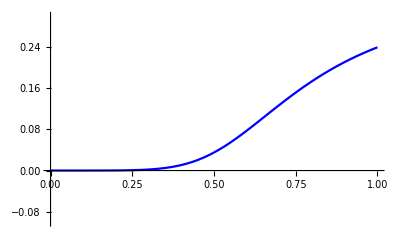

```mathematica
gamma5plot=Plot[gamma5CG,{a,0,1},PlotStyle->Blue,PlotRange->{{0,1},{-0.1,0.3}}]
```

```mathematica
gamma5EFTCAMBPlot=ListPlot[
dataEFTCAMB2ndOrder⟦All,{1,13}⟧
,Joined->False
,PlotMarkers->Automatic, PlotStyle->Red,PlotRange->{{0,1},{-0.1,0.3}}, PlotLabel->"Gamma5(a)"
]
```

-Graphics-

```mathematica
Show[gamma5EFTCAMBPlot,gamma5plot]
```

-Graphics-

#### gamma 5

```mathematica
gamma5prime = (4 (-1)^(-p (1+1/s)) p (1+s) (-2 Subscript[c, 5] s+Subscript[c, 4] p (1+s)) Subscript[χ, DS]^(-p (1+1/s)) ℋ[a]^(-1+(2 p (1+s))/s) φ'[a]^(-1+(2 p (1+s))/s) (ℋ[a] φ''[a]+φ'[a] ℋ'[a]))/s^2;
```

```mathematica
gamma5primeCG=gamma5prime/.DeSitterFP/.CGSubstitute/.Xds->7.613018601091973 H0^2 M^2/.c4->0.08485200961571562//Simplify;
```

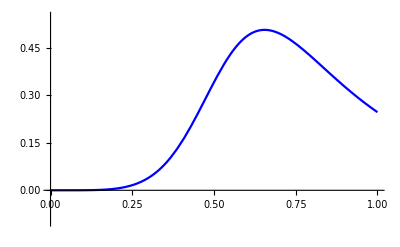

```mathematica
gamma5primeplot=Plot[gamma5primeCG,{a,0,1},PlotStyle->Blue,PlotRange->{{0,1},{-0.1,0.55}}]
```

```mathematica
gamma5primeEFTCAMBPlot=ListPlot[
dataEFTCAMB2ndOrder⟦All,{1,14}⟧
,Joined->False
,PlotMarkers->Automatic, PlotStyle->Red,PlotRange->{{0,1},{-0.1,0.55}}, PlotLabel->"Gamma5'(a)"
]
```

-Graphics-

```mathematica
Show[gamma5primeEFTCAMBPlot,gamma5primeplot]
```

-Graphics-

```mathematica
a:=A D[f[x],x]
```

```mathematica
a/.f'[x]->xf'[x]
```

A xf'[x]

```mathematica
-(adotoa**4*phip1**4*(-(a*self%WBGalileon_c4*eft_par_cache%h0_Mpc**2*m0)+6*self%WBGalileon_c5*(Hdot*phip1+a*adotoa**2*phip2)))/(2.*a*eft_par_cache%h0_Mpc**6*m0**5)
```

(3. A^2 m0 self^2 adotoa**4 phip1**4 h0_Mpc**2 WBGalileon_c4 WBGalileon_c5 (Hdot phip1+A phip2 adotoa**2 f'[x]) xf'[x]^2)/(m0**5 h0_Mpc**6)